Copied some code from my script code that ran on ACCRE, so it looks a little disorganized.

Version 2 implements best fit selection based on χ^2 test

Version 3 brings in more fits where I took some of the better fits and passed them through the NLMF function again

Version 4 looks at considering wound sizes from 0 to max wound size in plotting comparisons between model and data

Version 5 will go back to scaling +/- 50% wound size, but then look at the trends of each individual scale rather than scales of everything at once. Also try to get effective diffusion constants from model output directly

Version 6 is being made after first round of reviews on second submission. This version will add onto version 5 by including other analysis we want to put into revisions (GBP knockdown, possibly Mthl10 reduction, etc.)

# Model Equations

```mathematica
rd=10.;(* μm. spatial scale.*)
t0=47; (*s. median time for 2nd expansion signal to start from Erica's paper. *)
DL=260; (*μm^2/s. Estimated free diffusion constant of GBP*)
LRth =.5; (*Dimensionless. Ratio of [L.R] Subscript[to [R], T] needed for signal to be "on"*)
dr=.001; (*"small" r since we cannot use the origin in polar coordinates, μm*)
ρFar=1000/rd (*r that is "infinity" for numeric solving. scaled*);

(*Differential Equations*)
s=γd/γw^2*Exp[-(r-dr)^2/(2*γw^2)-γd*t];
dx=D[x[r,t],t]==(1+(γpL*yT[r,t])/(1+γP*x[r,t])^2)^-1*(γDP*Laplacian[x[r,t],{r,θ},"Polar"]+s+γc*γpL/γP*((γP*x[r,t])/(1+γP*x[r,t]))^2*yT[r,t]);
dyT=D[yT[r,t],t]==(-γc*γP*x[r,t]*yT[r,t])/(1+γP*x[r,t]);
dz=D[z[r,t],t]==(1+γR/(1+γL*z[r,t])^2)^-1*(γDL*Laplacian[z[r,t],{r,θ},"Polar"]+(γc*γP*x[r,t]*yT[r,t])/(1+γP*x[r,t]));

(*Initial Conditions and Boundary Conditions*)
initx=x[r,0]==0.; (*Initially no active protease*)
bc1x=(D[x[r,t],r]==0)/.r->dr; (*Radially symmetric --> no flux through origin*)
bc2x=x[ρFar,t]==0.; (*Concentration to 0 far away*)

inityT=yT[r,0]==1.; (*proligand initially exists at all points in space*)

initz=z[r,0]==0; (*Initially no ligand*)
bc1z=(D[z[r,t],r]==0)/.r->dr; (*Radially symmetric --> no flux through origin*)
bc2z=z[ρFar,t]==0.; (*Concentration to 0 far away*)

(*Put it all together*)
deqnsXY={dx,dyT,initx,bc1x,bc2x,inityT};
deqnsZ={dz,initz,bc1z,bc2z};
deqns=Join[deqnsXY,deqnsZ];
```

# Data

```mathematica
(*secondExpansionData is a list of elements for each data set {calcium radius at all times, calcium radius during second expansion, wound sizes*)
{dataAll,data2ndExp,woundSizes}=Transpose[Import["C:\\Users\\Greg Stevens\\Dropbox\\Research_Backup\\CurrentWork\\LigandModel\\Reviewer3\\SecondExpansionData.m"][[{1,15,17,19,20}]]];
scaledData=data2ndExp/.{t_?NumericQ,r_?NumericQ}->{t/t0,r/rd};

(*Add to data extra points for fitting*)
maxRads=MaximalBy[#,Last][[1,2]]&/@scaledData;
Δt=(#[[2,1]]-#[[1,1]])&/@scaledData;
scaledDataFitting=Table[Join[scaledData[[set]],Table[{scaledData[[set,-1,1]]+i*Δt[[set]],maxRads[[set]]},{i,Length@scaledData[[set]]}]],{set,Length@scaledData}];

(*Set max time to just be a little past this final data point. No need to go farther in time for fitting. Can look at farther time if inspecting particular parameter sets*)
τmaxes=(1.1*#[[;;,1]]//Last)&/@scaledDataFitting;
times=scaledDataFitting[[;;,;;,1]];(*Only need to pick out time points corresponding to the data*)
```

```mathematica
scaledDataAll=dataAll/.{t_?NumericQ,r_?NumericQ}->{t/t0,r/rd};
```

## Import Best Fit parameters

```mathematica
fitsTrial1=Table[(Import/@FileNames["C:\\Users\\Greg Stevens\\Dropbox\\Research_Backup\\CurrentWork\\LigandModel\\Reviewer3\\Fits to Five Sets\\Individual Fits\\set"<>ToString[set]<>"\\Analysis\\fit*.m"])[[;;,1]],{set,{1,15,17,19,20}}];
```

```mathematica
fitsTrial2=Table[Import/@FileNames["C:\\Users\\Greg Stevens\\Dropbox\\Research_Backup\\CurrentWork\\LigandModel\\Reviewer3\\Fits to Five Sets\\Individual Fits\\betterInits\\NLMF\\set"<>ToString[set]<>"\\analysis\\bestParams*.m"],{set,{1,15,17,19,20}}];

fitsTrial3=Table[Import/@FileNames["C:\\Users\\Greg Stevens\\Dropbox\\Research_Backup\\CurrentWork\\LigandModel\\Reviewer3\\Fits to Five Sets\\Individual Fits\\NLMF with Best Fits\\set"<>ToString[set]<>"\\bestParams*.m"],{set,{1,15,17,19,20}}];
```

```mathematica
fitParameters=DeleteDuplicates[#,Round[#1,.001]==Round[#2,.001]&]&/@Table[Join[fitsTrial1[[set]],fitsTrial2[[set]],fitsTrial3[[set]]],{set,Length@scaledDataFitting}];
```

# Some Functions

### Get / Undo Parameters

```mathematica
getParams[{ΓDP_,ΓDL_,Γd_,Γc_,ΓP_,ΓpL_,ΓL_,ΓR_,Γw_}]:=
{
γDP->12.22*10^#[[1]] ,(*Estimated from scales and DP 12.22 ≈ .1DL*)
γDL->t0/rd^2*DL*#[[2]], (*known value*)
γd->10^#[[3]] ,
γc->10^#[[4]],
γP->10^#[[5]],
γpL->10^#[[6]],
γL->10^#[[7]],
γR->10^#[[8]],
γw->#[[9]]
}&[{ΓDP,ΓDL,Γd,Γc,ΓP,ΓpL,ΓL,ΓR,Γw}];

undoParams[rules_]:=
{
Log[10,γDP/12.22],
rd^2/(t0*DL)*γDL,
Log[10,γd],
Log[10,γc],
Log[10,γP],
Log[10,γpL],
Log[10,γL],
Log[10,γR],
γw
}/.rules;
```

### Get Calcium Radius from Model Output

```mathematica
τmaxes[[1]]*t0
```

183.612

```mathematica
getRad//ClearAll
getRad[{ΓDP_,ΓDL_,Γd_,Γc_,ΓP_,ΓpL_,ΓL_,ΓR_,Γw_},set_]:=getRad[{ΓDP,ΓDL,Γd,Γc,ΓP,ΓpL,ΓL,ΓR,Γw},set]=
Block[{params,soln,rStep,points,interps,rads,maxes},
params=getParams[{ΓDP,ΓDL,Γd,Γc,ΓP,ΓpL,ΓL,ΓR,Γw}];

soln=NDSolveValue[deqns/.params,z,{r,dr,ρFar},{t,0,τmaxes[[set]]},Method->{"IndexReduction"->Automatic,"EquationSimplification"->"Residual","PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->200,"MaxPoints"->500,"DifferenceOrder"->2}}}];

(*Check if maximum ever gets above threshold*)
maxes=((γL*soln[dr,#])/(1+γL*soln[dr,#]))/.params&/@times[[set]];

(*Find Ligand radius v. time points. Replace negative/ no solution cases with 0, and use a better (but longer) solving method if points are bad (just in case)*)
rads=
Table[
{times[[set,i]],If[maxes[[i]]<0.5,0.,r/.FindRoot[(((γL*soln[r,times[[set,i]]])/(1+γL*soln[r,times[[set,i]]]))/.params)==.5,{r,dr,ρFar}]]},
{i,Length@times[[set]]}];

Return[rads];
]

(*Failed expression for when errors are thrown*)
failedExpression=scaledDataFitting/.{x_,y_}->{x,0};

(*getRadFit function is similar to getRad function, for the later time points it sets the output equal to the constraint data if it is below it so that there is no peanalty for going below the constraint*)
getRadFit//ClearAll
getRadFit[{ΓDP_,ΓDL_,Γd_,Γc_,ΓP_,ΓpL_,ΓL_,ΓR_,Γw_},set_]:=getRadFit[{ΓDP,ΓDL,Γd,Γc,ΓP,ΓpL,ΓL,ΓR,Γw},set]=
Catch[
TimeConstrained[
Block[{params,soln,rStep,points,interps,rads,rads1,maxes},
params=getParams[{ΓDP,ΓDL,Γd,Γc,ΓP,ΓpL,ΓL,ΓR,Γw}];

soln=Check[

NDSolveValue[deqns/.params,z,{r,dr,ρFar},{t,0,τmaxes[[set]]},Method->{"IndexReduction"->Automatic,"EquationSimplification"->"Residual","PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->200,"MaxPoints"->500,"DifferenceOrder"->2}}}],

Throw[failedExpression[[set]]],

{NDSolveValue::eerr,NDSolveValue::ndsz}
];

(*Check if maximum ever gets above threshold*)
maxes=Check[((γL*soln[dr,#])/(1+γL*soln[dr,#]))/.params&/@times[[set]],Throw[failedExpression[[set]]],{Power::infy}];

(*Find Ligand radius v. time points. Replace negative/ no solution cases with 0, and use a better (but longer) solving method if points are bad (just in case)*)
rads1=
Table[
If[maxes[[i]]<0.5,0.,r/.Check[FindRoot[(((γL*soln[r,times[[set,i]]])/(1+γL*soln[r,times[[set,i]]]))/.params)==.5,{r,dr,ρFar}],Throw[failedExpression[[set]]],{FindRoot::cvmit,FindRoot::nlnum,FindRoot::brmp,Power::infy}]],
{i,Length@times[[set]]}];

(*Replace all points in the latter half with the constraint data value if they are below it*)
rads=Table[
{times[[set,i]],If[i>Length[times[[set]]]/2&&rads1[[i]]<=maxRads[[set]],maxRads[[set]],rads1[[i]]]}
,{i,Length@times[[set]]}];

Return[rads];
],
4,
Throw[failedExpression[[set]]]
]
]
```

```mathematica
(*Function for getting Ca rad v. time for wound scaled trials where we are now no longer comparing directly to the data. Therefore, we can no longer just use the time points found in the data*)
getRadAll//ClearAll
getRadAll[{ΓDP_,ΓDL_,Γd_,Γc_,ΓP_,ΓpL_,ΓL_,ΓR_,Γw_}]:=getRadAll[{ΓDP,ΓDL,Γd,Γc,ΓP,ΓpL,ΓL,ΓR,Γw}]=
Block[{params,soln,points,rads,maxes,allTimes=Range[0.,2.*Max@τmaxes,2.*Max@τmaxes/499.]},
params=getParams[{ΓDP,ΓDL,Γd,Γc,ΓP,ΓpL,ΓL,ΓR,Γw}];

soln=NDSolveValue[deqns/.params,z,{r,dr,ρFar},{t,0,2*Max@τmaxes},Method->{"IndexReduction"->Automatic,"EquationSimplification"->"Residual","PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->200,"MaxPoints"->500,"DifferenceOrder"->2}}}];

(*Check if maximum ever gets above threshold*)
maxes=((γL*soln[dr,#])/(1+γL*soln[dr,#]))/.params&/@allTimes;

(*Find Ligand radius v. time points. Replace negative/ no solution cases with 0, and use a better (but longer) solving method if points are bad (just in case)*)
rads=
Table[
{allTimes[[i]],If[maxes[[i]]<0.5,0.,r/.FindRoot[(((γL*soln[r,allTimes[[i]]])/(1+γL*soln[r,allTimes[[i]]]))/.params)==.5,{r,dr,ρFar}]]},
{i,Length@allTimes}];

Return[rads];
]
```

### Get Start Time

```mathematica
getStartTime[{ΓDPP_,ΓDLP_,ΓdP_,ΓcP_,ΓPP_,ΓpLP_,ΓLP_,ΓRP_,ΓwP_}]:=
Block[{params=getParams[{ΓDPP,ΓDLP,ΓdP,ΓcP,ΓPP,ΓpLP,ΓLP,ΓRP,ΓwP}],soln,stime=0.},

soln=NDSolveValue[Join[deqns,{WhenEvent[(((γL*z[dr,t])/(1+γL*z[dr,t]))/.params)≥0.5,stime=t;"StopIntegration"]}]/.params,z,{r,dr,ρFar},{t,0.,Max@τmaxes},Method->{"IndexReduction"->Automatic,"EquationSimplification"->"Residual","PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->200,"MaxPoints"->500,"DifferenceOrder"->2}}}];

Return[stime];]
```

# Pick out only best fits from each trial

Use χ^2 test to determine which fits are not distinguishable from the best fit. Only compare to actual data values, not constraint points from fitting

```mathematica
getSumSquare[params_,set_]:=Total[(getRadFit[params,set][[;;(Length@times[[set]])/2,2]]-scaledData[[set,;;,2]])^2]
```

```mathematica
ssds=Quiet@Table[getSumSquare[#,set]&/@fitParameters[[set]],{set,Length@scaledDataFitting}]
```

{{11.5632,7.47393,37.7182,2903.37,5.66246,2903.37,2903.37,2903.37,14.1771,12.3245,2903.37,0.486086,2.77147,6.21346,1.15531,8.512,16.4318,13.9058,15.0489,12.7462,1.00245,1.03874,15.541,15.4156,1.33619,15.4989,14.2487,18.7917,19.1454,1.09273,1.09831,1.31073},{26.9666,2.65584,26.1652,6931.48,33.2871,6931.48,4.82682,2.37485,3.76309,10.7161,48.7434,16.9725,2.35803,7.81523,9.20797,4.16905,74.7954,82.8646,61.4569,37.4025,1.83568,27.153,49.4364,3.11297,6931.48,22.2073,27.6284,22.9577,70.2273,25.9362,25.6425,2.17501,1.52981,2.08475,3.1084,1.50944,3.70548,1.42113},{2.27749,1969.7,13.1285,15.9505,0.348653,1969.7,5.55192,1969.7,1.65431,1969.7,1.1405,0.490032,5.9897,6.63829,1969.7,0.0737742,22.6855,14.9641,23.116,18.9224,13.5628,7.51649,2.08583,0.0825768,24.5659,25.8712,24.7521,19.1403,22.6142,27.2332,0.0866868,5.61349,1.16913,13.8989},{2.09799,2.39194,2.49474,2.8597,1.53458,1.42342,2.30463,1.01627,2.42784,554.119,2.62918,0.87929,2.15828,2.16561,3.87694,3.3591,3.80995,1.43429,3.00147,2.42111,0.955422,3.23105,2.74329,3.44147,0.982168,3.37179,0.525126,3.9517,0.522052,0.781247,0.999266,0.982272,1.34785},{0.664707,0.256425,0.673509,0.727779,0.0723017,0.143424,0.0409007,0.577377,0.0919869,0.857598,0.707044,0.338379,0.858576,1.04355,0.609716,1.00965,0.6343,0.0557913,0.84063,0.393879,0.956632,0.620652,0.957103,0.758744,0.0714052,104.469,1.01259,0.938369,104.469,104.469,0.0715711,104.469,0.0880522,0.119825,0.0900254,0.0928766}}

```mathematica
(*get best SSR for each data set*)
bestSSRs=Transpose@Table[RankedMin[#,num]&/@ssds,{num,3}]
```

{{0.486086,1.00245,1.03874},{1.42113,1.50944,1.52981},{0.0737742,0.0825768,0.0866868},{0.522052,0.525126,0.781247},{0.0409007,0.0557913,0.0714052}}

```mathematica
(*get pvalues*)
vs=(Length@#-Length@fitParameters[[1,1]])&/@scaledData
pVals=Table[ 1-CDF[ChiSquareDistribution[vs[[set]]],vs[[set]]*ssds[[set,fit]]/bestSSRs[[set,num]]],{num,3},{set,Length@scaledData},{fit,Length@fitParameters[[set]]}];
```

{19,27,19,6,1}

General::munfl: Exp[-56649.9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
bestPos=DeleteDuplicates/@Flatten/@Transpose[Table[Flatten[Position[#,x_/;x≥.05]&/@pVals[[num]],{3}],{num,3}],{3,2,1}]
```

{{12,15,21,22,25,30,31,32},{21,33,34,36,38,32},{16,24,31},{8,12,21,25,27,29,30,31,32,5,6,18,33},{5,6,7,9,18,25,31,33,34,35,36,2}}

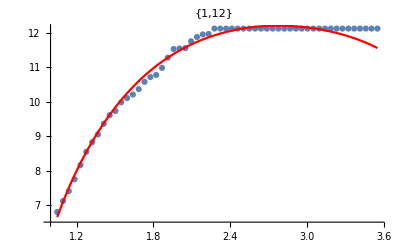
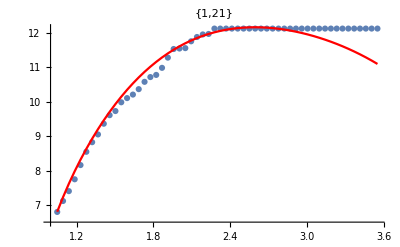
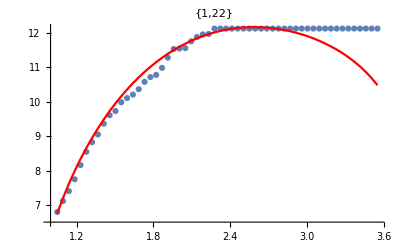
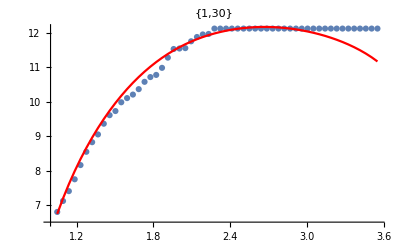
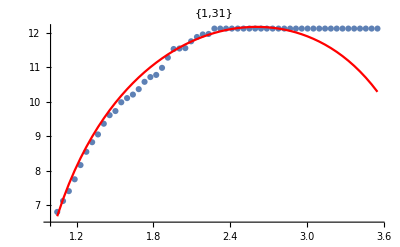
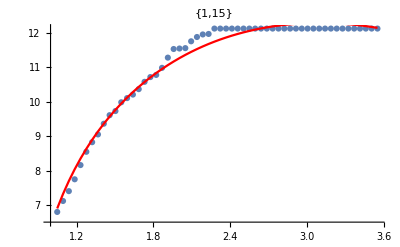
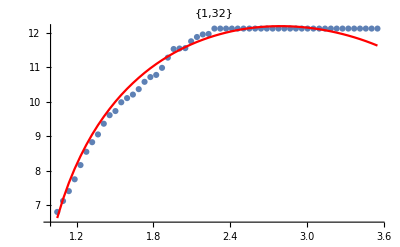
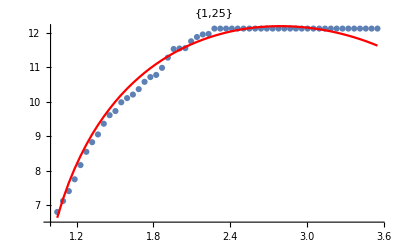
{{{{0.456836,0.969771,0.975243},-Graphics-},{{0.00418187,0.456836,0.50009},-Graphics-},{{0.00272585,0.413584,0.456836},-Graphics-},{{0.00141903,0.352988,0.39533},-Graphics-},{{0.00132499,0.347009,0.389201},-Graphics-},{{0.000651258,0.289405,0.32954},-Graphics-},{{0.000086098,0.165778,0.197109},-Graphics-},{{0.0000611474,0.150107,0.179785},-Graphics-},{{1.62093×10^-14,0.0000551132,0.000103519},-Graphics-},{{0.,2.4758×10^-14,1.20015×10^-13},-Graphics-},{{0.,3.33067×10^-16,1.66533×10^-15},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-}},{{{0.463795,0.550912,0.569873},-Graphics-},{{0.376699,0.463795,0.48332},-Graphics-},{{0.357763,0.44427,0.463795},-Graphics-},{{0.142036,0.202548,0.217653},-Graphics-},{{0.0557258,0.0897662,0.0989747},-Graphics-},{{0.0383342,0.0646237,0.0719429},-Graphics-},{{0.0170683,0.0316014,0.0358877},-Graphics-},{{0.0157942,0.0294982,0.0335613},-Graphics-},{{0.00402721,0.00871279,0.0102281},-Graphics-},{{0.000350246,0.000964652,0.00119229},-Graphics-},{{0.000341275,0.000942255,0.00116521},-Graphics-},{{9.83385×10^-6,0.0000374239,0.0000495653},-Graphics-},{{6.84748×10^-6,0.0000268898,0.0000358536},-Graphics-},{{4.97647×10^-7,2.43948×10^-6,3.41076×10^-6},-Graphics-},{{5.6788×10^-9,3.99415×10^-8,6.03317×10^-8},-Graphics-},{{0.,0.,1.11022×10^-16},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-}},{{{0.456836,0.591587,0.645919},-Graphics-},{{0.322235,0.456836,0.515824},-Graphics-},{{0.268355,0.397854,0.456836},-Graphics-},{{3.60925×10^-11,1.70323×10^-9,7.64372×10^-9},-Graphics-},{{0.,2.44249×10^-15,2.38698×10^-14},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-}},{{{0.42319,0.427135,0.675407},-Graphics-},{{0.419245,0.42319,0.672213},-Graphics-},{{0.174766,0.17776,0.42319},-Graphics-},{{0.120268,0.122702,0.344297},-Graphics-},{{0.088973,0.0909919,0.290745},-Graphics-},{{0.0798686,0.0817502,0.273524},-Graphics-},{{0.079835,0.0817161,0.273459},-Graphics-},{{0.0745035,0.0763002,0.262941},-Graphics-},{{0.0694994,0.0712139,0.252744},-Graphics-},{{0.0167633,0.0173617,0.110608},-Graphics-},{{0.011949,0.0124061,0.0905036},-Graphics-},{{0.0113771,0.0118165,0.0879025},-Graphics-},{{0.00720619,0.00750912,0.066926},-Graphics-},{{0.000497977,0.000528657,0.0131622},-Graphics-},{{0.000370989,0.000394634,0.0109761},-Graphics-},{{0.000357904,0.000380808,0.0107353},-Graphics-},{{0.000180593,0.00019304,0.00702839},-Graphics-},{{0.000117145,0.000125583,0.00537072},-Graphics-},{{0.000101322,0.000108725,0.0049068},-Graphics-},{{0.0000979792,0.000105162,0.00480535},-Graphics-},{{0.0000701682,0.0000754803,0.00390231},-Graphics-},{{0.000035738,0.0000386162,0.00255944},-Graphics-},{{0.0000200848,0.0000217851,0.00178327},-Graphics-},{{0.0000111227,0.0000121113,0.0012299},-Graphics-},{{5.39453×10^-6,5.90187×10^-6,0.000779448},-Graphics-},{{1.65754×10^-6,1.8274×10^-6,0.000369532},-Graphics-},{{8.548×10^-7,9.46439×10^-7,0.000242781},-Graphics-},{{8.00395×10^-7,8.86578×10^-7,0.000232851},-Graphics-},{{5.57514×10^-7,6.18987×10^-7,0.00018505},-Graphics-},{{8.14259×10^-8,9.15261×10^-8,0.0000543032},-Graphics-},{{5.72854×10^-8,6.45359×10^-8,0.0000433746},-Graphics-},{{3.86658×10^-8,4.36689×10^-8,0.0000337332},-Graphics-},{{0.,0.,0.},-Graphics-}},{{{0.317311,0.39188,0.44915},-Graphics-},{{0.242834,0.317311,0.376734},-Graphics-},{{0.186403,0.257925,0.317311},-Graphics-},{{0.185892,0.257372,0.316749},-Graphics-},{{0.183662,0.254958,0.314291},-Graphics-},{{0.142307,0.209014,0.266798},-Graphics-},{{0.137915,0.203985,0.261506},-Graphics-},{{0.133698,0.199127,0.256373},-Graphics-},{{0.131833,0.196968,0.254086},-Graphics-},{{0.0869661,0.14278,0.195178},-Graphics-},{{0.061123,0.108858,0.15641},-Graphics-},{{0.0122838,0.032044,0.0580891},-Graphics-},{{0.00402347,0.013788,0.0294887},-Graphics-},{{0.0019141,0.00788297,0.0188421},-Graphics-},{{0.00011293,0.000946957,0.00347652},-Graphics-},{{0.0000980125,0.000851936,0.00319615},-Graphics-},{{0.0000821434,0.000746735,0.00287821},-Graphics-},{{0.0000554588,0.000557086,0.00228038},-Graphics-},{{0.0000495062,0.000511868,0.00213208},-Graphics-},{{0.0000321404,0.000370972,0.00165113},-Graphics-},{{0.0000246183,0.00030415,0.00141033},-Graphics-},{{0.0000165428,0.000226224,0.00111515},-Graphics-},{{5.80042×10^-6,0.00010374,0.000601068},-Graphics-},{{4.67067×10^-6,0.0000883091,0.000529076},-Graphics-},{{4.61272×10^-6,0.0000874933,0.000525201},-Graphics-},{{1.6691×10^-6,0.0000411137,0.000288833},-Graphics-},{{1.32324×10^-6,0.0000346027,0.000251997},-Graphics-},{{1.31533×10^-6,0.0000344491,0.000251112},-Graphics-},{{6.74902×10^-7,0.0000209935,0.000169717},-Graphics-},{{6.50193×10^-7,0.0000204205,0.000166043},-Graphics-},{{4.39131×10^-7,0.000015262,0.000131898},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-},{{0.,0.,0.},-Graphics-}}}

```mathematica
Reverse/@(SortBy[#,First]&/@(Quiet@Table[{pVals[[;;,set,fit]],Show[ListPlot[scaledDataFitting[[set]],PlotRange->All,PlotLabel->{set,fit}],ListLinePlot[getRad[fitParameters[[set,fit]],set],PlotRange->All,PlotStyle->Red]]},{set,Length@scaledDataFitting},{fit,Length@fitParameters[[set]]}]))
```

```mathematica
bestFitParameters=Table[fitParameters[[set,bestPos[[set]]]],{set,Length@scaledData}];
```

```mathematica
SmoothHistogram[Log[10,t0/Flatten[γd/.Map[getParams,bestFitParameters[[;;4]],{2}]]],AxesLabel->{"Log[τd]",None}]
```

-Graphics-

```mathematica
(*Export["C:\\Users\\Greg Stevens\\Dropbox\\Research_Backup\\CurrentWork\\NewCalciumModel\\Second Expansion\\LRParams.m",Map[getParams,bestFitParameters,{2}][[1;;4]]];*)
```

# 2nd expansion measures

Look at the 2nd expansion diffusion rate and start times

## Data

Be careful about the two different t0’s. The imported list t0s corresponds to the start of the second expansion in the data. the t0andDiff list corresponds to the back-propogated start time from the delayed diffusion fit

```mathematica
ddparams=Import["C:\\Users\\Greg Stevens\\Dropbox\\Research_Backup\\CurrentWork\\LigandModel\\Hutson_2ndExp_Analysis\\t0andDiff.m"];
t0s=Import["C:\\Users\\Greg Stevens\\Dropbox\\Research_Backup\\CurrentWork\\LigandModel\\Hutson_2ndExp_Analysis\\t0s.m"];
```

```mathematica
woundSizesAll={35.7,29.1,36.7,44.8,41,38.4,40.3,52.8,53.4,71.9,66.3,28.2,45.3,54.5,65.1,20.3,21.9,29.1,28.5,4.3,5.6,49.6,33.4,37.8,41.5,49.1,38.9,14.2};
```

```mathematica
t0andDiff={t0,α}/.ddparams
```

{{37.8021,24.907},{42.3625,5.39066},{38.3616,11.0392},{22.2343,10.9802},{24.3927,83.2308},{26.4202,5.32699},{26.1241,22.4766},{20.8858,9.14155},{52.9959,24.6639},{32.4251,73.2189},{21.4315,33.2992},{91.3683,17.0041},{45.5226,20.8425},{61.9391,31.226},{53.0032,41.4931},{80.7337,1.31876},{57.7508,19.0603},{46.6886,2.5687},{183.131,16.8637},{32.8252,3.92576},{4.57705,0.209378},{61.403,31.4755},{54.1745,26.0313},{48.2289,37.3625},{47.9941,20.8195},{69.1206,19.9367},{60.167,28.6536},{122.602,4.03858}}

```mathematica
αErrors=Import["C:\\Users\\Greg Stevens\\Dropbox\\Research_Backup\\CurrentWork\\LigandModel\\Hutson_2ndExp_Analysis\\αErrors.m"];
σ0Errors=Import["C:\\Users\\Greg Stevens\\Dropbox\\Research_Backup\\CurrentWork\\LigandModel\\Hutson_2ndExp_Analysis\\σ0Errors.m"];
```

```mathematica
αs=Table[Around[t0andDiff[[i,2]],αErrors[[i]]],{i,Length@αErrors}]
```

{24.91.6,5.4.,11.02.6,11.4.,83.6.,5.13.,22.52.6,9.8.,25.9.,73.5.,33.8.,17.01.1,21.4.,31.20.9,41.52.5,1.30.8,19.10.8,2.63.4,17.4.,3.92.1,0.5.,31.10.,26.01.2,37.41.2,20.80.8,19.93.5,28.71.0,4.00.7}

```mathematica
tStarts=Table[
AroundReplace[t-σ0^2/(2*α),
{t->Around[t0s[[i]],0],
σ0->Around[σ0/.ddparams[[i]],σ0Errors[[i]]],
α->Around[α/.ddparams[[i]],αErrors[[i]]]}
],
{i,Length@t0s}]
```

{37.80.8,42.41.4,38.42.2,22.5.,24.40.8,26.51.,26.10.9,21.31.,53.6.,32.41.3,21.6.,91.40.9,46.8.,61.90.8,53.01.1,81.28.,57.80.5,47.26.,183.12.9,32.83.2,0.01.810^3,61.5.,54.20.8,48.20.6,48.01.2,69.9.,60.20.8,122.61.6}

```mathematica
ListPlot[Partition[Riffle[woundSizesAll,αs],2],PlotRange->{{0,All},{0,All}},AxesLabel->Reverse@{"Effective Diffusion Constant (μm^2/s)","Wound Diameter (μm)"},ImageSize->Large]
ListPlot[Partition[Riffle[woundSizesAll,tStarts],2],PlotRange->{{0,All},{0,All}},AxesLabel->Reverse@{"Start Time (s)","Wound Diameter (μm)"},ImageSize->Large]
```

-Graphics-

-Graphics-

```mathematica
(*Look at Max Rad*)
maxRadsData=Transpose[Import["C:\\Users\\Greg Stevens\\Dropbox\\Research_Backup\\CurrentWork\\LigandModel\\Reviewer3\\SecondExpansionData.m"]][[2]][[;;,-1,2]]
```

{121.24,126.617,87.4339,129.559,132.029,114.153,110.616,145.844,119.643,135.952,124.311,94.027,133.5,120.78,161.855,65.8354,99.9831,86.741,68.5592,38.0759,31.4954,121.3,129.324,138.773,116.163,113.339,116.789,75.0807}

```mathematica
ListPlot[Partition[Riffle[woundSizesAll,maxRadsData],2],AxesLabel->{"Wound Diamater (μm)","2nd Exp. Max Radius (μm)"}]
```

-Graphics-

### Data Fits

```mathematica
(*Fits Linear, Quadratic, Cubic*)
αFitData=LinearModelFit[Partition[Riffle[woundSizesAll,αs[[;;,1]]],2]/.{w_,t_}/;w<15->Nothing,w,w];timeFitData=NonlinearModelFit[Partition[Riffle[woundSizesAll,tStarts[[;;,1]]],2]/.{w_,t_}/;w<15->Nothing,a/w+b,{a,b},w];
```

```mathematica
Show[
ListPlot[Partition[Riffle[woundSizesAll,αs],2]/.{w_,t_}/;w<15->Nothing,
PlotRange->{{15,All},{0,All}},
ImageSize->Large,
PlotStyle->Black,
Axes->None,
Frame->{{True,False},{True,False}},
FrameLabel->{{"Effective Diffusion Constant (μm^2/s)",False},{"Wound Diameter (μm)",False}},
FrameStyle->Directive[Black,18]],

Plot[Normal[αFitData],{w,15,75},PlotStyle->Red],

Plot[Evaluate[αFitData["SinglePredictionBands"]],{w,15,75},Filling->{1->{{2},Opacity[.1,Red]}},PlotStyle->None]]

Show[
ListPlot[Partition[Riffle[woundSizesAll,tStarts],2]/.{w_,t_}/;w<15->Nothing,
PlotRange->{{15,All},{0,All}},
ImageSize->Large,
PlotStyle->Black,
Axes->None,
Frame->{{True,False},{True,False}},
FrameLabel->{{"Start Time (s)",False},{"Wound Diameter (μm)",False}},
FrameStyle->Directive[Black,18]],

Plot[Normal[timeFitData],{w,15,75},PlotStyle->Red],

Plot[Evaluate[timeFitData["SinglePredictionBands"]],{w,15,75},Filling->{1->{{2},Opacity[.1,Red]}},PlotStyle->None]]
```

-Graphics-

-Graphics-

```mathematica
αFitData["ParameterTable"]
timeFitData["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -7.56064 | 11.282 | -0.670152 | 0.509434
w | 0.766275 | 0.255574 | 2.99826 | 0.00641654

| Estimate | Standard Error | t-Statistic | P-Value
a | 1545.44 | 700.3 | 2.20683 | 0.0375798
b | 11.7021 | 19.3696 | 0.604146 | 0.55166

```mathematica
ListPlot[(Partition[Riffle[woundSizesAll,tStarts],2]/.{w_,t_}/;w<15->Nothing)/.{w_,t_}->{1/w,t},
PlotRange->All,
ImageSize->Large,
PlotStyle->Black,
Axes->None,
Frame->{{True,False},{True,False}},
FrameLabel->{{"Start Time (s)",False},{"Wound Diameter (μm)",False}},
FrameStyle->Directive[Black,18]]
```

-Graphics-

## Model

### Wound Scaled Parameter Sets

```mathematica
woundScales=Table[size,{set,Length@woundSizes},{size,.5,1.5,.1}]
```

{{0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5},{0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5},{0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5},{0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5},{0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5}}

```mathematica
(*Order of indices: [[dataset, fit, scale, parameter]]*)
woundScaledParams=Table[undoParams[getParams[bestFitParameters[[set,fit]]]/.{(γw->x_)->(γw->scale*x),(γP->x_)->(γP->x*scale^2)}],{set,Length@bestFitParameters},{fit,Length@bestFitParameters[[set]]},{scale,woundScales[[set]]}];
```

```mathematica
(*scaled wounds based on measured wound size for each dataset*)
woundSizes
```

{35.7,65.1,21.9,28.5,4.3}

```mathematica
scaledWoundSizes=woundSizes*woundScales
```

{{17.85,21.42,24.99,28.56,32.13,35.7,39.27,42.84,46.41,49.98,53.55},{32.55,39.06,45.57,52.08,58.59,65.1,71.61,78.12,84.63,91.14,97.65},{10.95,13.14,15.33,17.52,19.71,21.9,24.09,26.28,28.47,30.66,32.85},{14.25,17.1,19.95,22.8,25.65,28.5,31.35,34.2,37.05,39.9,42.75},{2.15,2.58,3.01,3.44,3.87,4.3,4.73,5.16,5.59,6.02,6.45}}

### Take out Bad Solutions that give errors for wound scaled parameter sets

```mathematica
(*Get the maximum calcium radius for each run*)
maxPoints=Quiet@Map[MaximalBy[getRadAll[#],Last,1][[1]]&,woundScaledParams,{3}];
```

```mathematica
Table[ListLinePlot[getRadAll/@woundScaledParams[[set,fit]],PlotRange->{0.,45.},PlotLabel->"set "<>ToString[set]<>" fit "<>ToString[fit],Epilog->Point/@maxPoints[[set,fit]]],{set,Length@woundScaledParams},{fit,Length@woundScaledParams[[set]]}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
(*Throw out bad solutions*)
bestFitParametersGood=Delete[bestFitParameters,{{2,6},{4,1},{4,10},{4,11},{4,12},{5,3}}];
```

```mathematica
(*Take out parameters that are very similar*)
bestFitParametersGood=DeleteDuplicates[#,Round[#1,1]==Round[#2,1]&]&/@bestFitParametersGood;
```

```mathematica
(*Take out parameters that given no response*)
woundScaledParamsWithScales=

Block[{params},
Table[

params=undoParams[getParams[bestFitParametersGood[[set,fit]]]/.{(γw->x_)->(γw->scale*x),(γP->x_)->(γP->x*scale^2)}];

If[getRadAll[params][[;;,2]]≠ConstantArray[0.,Length@getRadAll[params]],
{scale,params},Nothing
],

{set,Length@bestFitParametersGood},
{fit,Length@bestFitParametersGood[[set]]},
{scale,.5,1.5,.1}]

];
```

```mathematica
(*Order of indices: [[dataset, scale, fit, parameter]]*)
(*woundScaledParams=Table[undoParams[getParams[bestFitParametersGood[[set,fit]]]/.{(γw->x_)->(γw->scale*x),(γP->x_)->(γP->x*scale^2)}],{set,Length@bestFitParametersGood},{fit,Length@bestFitParametersGood[[set]]},{scale,.5,1.5,.1}];*)

woundScaledParams=woundScaledParamsWithScales[[;;,;;,;;,2]];
```

```mathematica
scaledWoundSizes=Table[woundSizes[[set]]*woundScaledParamsWithScales[[set,fit,scale,1]],{set,Length@woundScaledParams},{fit,Length@woundScaledParams[[set]]},{scale,Length@woundScaledParams[[set,fit]]}];

maxPoints=Map[MaximalBy[getRadAll[#],Last,1][[1]]&,woundScaledParams,{3}];
```

```mathematica
Table[ListLinePlot[getRadAll/@woundScaledParams[[set,fit]],PlotRange->{0.,45.},PlotLabel->"set "<>ToString[set]<>" fit "<>ToString[fit],Epilog->Point/@maxPoints[[set,fit]]],{set,Length@woundScaledParams},{fit,Length@woundScaledParams[[set]]}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

### Start Times

```mathematica
startTimes=Quiet@Map[getStartTime,woundScaledParams,{3}];
```

```mathematica
startTimesvWound=Table[{scaledWoundSizes[[set,fit,scale]],startTimes[[set,fit,scale]]*t0},{set,Length@startTimes},{fit,Length@startTimes[[set]]},{scale,Length@startTimes[[set,fit]]}];
```

```mathematica
Show[
ListPlot[Partition[Riffle[woundSizesAll,tStarts],2],PlotRange->{{0,All},{0,All}},PlotStyle->Black,AxesLabel->{"Wound Diameter (μm)","2nd Exp. Start Time (s)"},ImageSize->Large],
ListLinePlot[startTimesvWound[[1]]/.{w_,0.}->Nothing,PlotRange->All,PlotStyle->Red],
ListLinePlot[startTimesvWound[[2]]/.{w_,0.}->Nothing,PlotRange->All,PlotStyle->Orange],
ListLinePlot[startTimesvWound[[3]]/.{w_,0.}->Nothing,PlotRange->All,PlotStyle->Green],
ListLinePlot[startTimesvWound[[4]]/.{w_,0.}->Nothing,PlotRange->All,PlotStyle->Blue],
ListLinePlot[startTimesvWound[[5]]/.{w_,0.}->Nothing,PlotRange->All,PlotStyle->Purple],
ListPlot[Partition[Riffle[woundSizesAll,tStarts],2],PlotRange->{{0,All},{0,All}},PlotStyle->Black,AxesLabel->{"Wound Diameter (μm)","2nd Exp. Start Time (s)"},ImageSize->Large],
Graphics[Join[{PointSize[Large]},Riffle[{Red,Orange,Green,Blue,Purple},Point/@Partition[Riffle[woundSizesAll,tStarts[[;;,1]]],2][[{1,15,17,19,20}]]]]]]
```

-Graphics-

### Max Rads

```mathematica
maxRadsvWound=Table[{scaledWoundSizes[[set,fit,scale]],maxPoints[[set,fit,scale,2]]*rd},{set,Length@startTimes},{fit,Length@startTimes[[set]]},{scale,Length@startTimes[[set,fit]]}];
```

```mathematica
Show[
ListPlot[Partition[Riffle[woundSizesAll,maxRadsData],2],PlotRange->{{0,All},{0,All}},PlotStyle->Black,AxesLabel->{"Wound Diameter (μm)","2nd Exp. Max Rad (μm)"},ImageSize->Large],
ListLinePlot[maxRadsvWound[[1]]/.{w_,0.}->Nothing,PlotRange->All,PlotStyle->Red],
ListLinePlot[maxRadsvWound[[2]]/.{w_,0.}->Nothing,PlotRange->All,PlotStyle->Orange],
ListLinePlot[maxRadsvWound[[3]]/.{w_,0.}->Nothing,PlotRange->All,PlotStyle->Green],
ListLinePlot[maxRadsvWound[[4]]/.{w_,0.}->Nothing,PlotRange->All,PlotStyle->Blue],
ListLinePlot[maxRadsvWound[[5]]/.{w_,0.}->Nothing,PlotRange->All,PlotStyle->Purple],
ListPlot[Partition[Riffle[woundSizesAll,maxRadsData],2],PlotRange->{{0,All},{0,All}},PlotStyle->Black,ImageSize->Large],
Graphics[Join[{PointSize[Large]},Riffle[{Red,Orange,Green,Blue,Purple},Point/@Partition[Riffle[woundSizesAll,maxRadsData],2][[{1,15,17,19,20}]]]]]]
```

-Graphics-

### Get Needed List Positions

```mathematica
(*Get position in rad v. time list of maximum ca rad*)
maxPos=Table[First@First@Position[getRadAll[woundScaledParams[[set,fit,scale]]],maxPoints[[set,fit,scale]]],{set,Length@woundScaledParams},{fit,Length@woundScaledParams[[set]]},{scale,Length@woundScaledParams[[set,fit]]}];
```

```mathematica
(*Get position in rad v. time list where the radius is first non-zero*)
t0Pos=Table[
Block[{flag=False,pos=1,startPos=1},
While[!flag&&pos≤Length@getRadAll[woundScaledParams[[set,fit,scale]]],
If[getRadAll[woundScaledParams[[set,fit,scale]]][[pos,2]]≠0.,flag=True; startPos=pos;];
pos+=1;
];
startPos
]
,{set,Length@woundScaledParams},{fit,Length@woundScaledParams[[set]]},{scale,Length@woundScaledParams[[set,fit]]}];
```

```mathematica
tEndPos=Table[
Block[{flag=False,pos=-1,endPos=-1},
While[!flag&&-pos≤Length@getRadAll[woundScaledParams[[set,fit,scale]]],
If[getRadAll[woundScaledParams[[set,fit,scale]]][[pos,2]]≠0.,flag=True; endPos=pos;];
pos-=1;
];
endPos
]
,{set,Length@woundScaledParams},{fit,Length@woundScaledParams[[set]]},{scale,Length@woundScaledParams[[set,fit]]}];
```

### Diffusion Constants from Model Output

The second derivative of the R^2 function is -(8 α^2)/(2*α*(t-t_0)+σ_0^2). However, if we set t0 to be right at the time when the signal appears, then σ0 = 0, and we can then find α as a function of time very simply. Of course, the DD model assumes a constant diffusion constant, but we can think of this as a “local” diffusion constant with respect to time.

Try on one output for now...

```mathematica
secondDerivs=Map[D[Interpolation[getRadAll[#]][t],{t,2}]&,woundScaledParams,{3}];
```

```mathematica
αsAlg=Table[(rd^2/t0)*NIntegrate[-0.25*(t-startTimes[[set,fit,scale]])*secondDerivs[[set,fit,scale]],{t,1.001*#[[1]],.999*#[[2]]}]/(.999*#[[2]]-1.001*#[[1]])&[getRadAll[woundScaledParams[[set,fit,scale]]][[{t0Pos[[set,fit,scale]],tEndPos[[set,fit,scale]]},1]]],{set,Length@secondDerivs},{fit,Length@secondDerivs[[set]]},{scale,Length@secondDerivs[[set,fit]]}];
```

```mathematica
αsvWound=Table[{scaledWoundSizes[[set,fit,scale]],αsAlg[[set,fit,scale]]},{set,Length@startTimes},{fit,Length@startTimes[[set]]},{scale,Length@startTimes[[set,fit]]}];
```

```mathematica
Show[
ListPlot[Partition[Riffle[woundSizesAll,αs],2],PlotRange->{{0,All},{0,All}},PlotStyle->Black,AxesLabel->{"Wound Diameter (μm)","2nd Exp. Max Rad (μm)"},ImageSize->Large],
ListLinePlot[αsvWound[[1]]/.{w_,0.}->Nothing,PlotRange->All,PlotStyle->Red],
ListLinePlot[αsvWound[[2]]/.{w_,0.}->Nothing,PlotRange->All,PlotStyle->Orange],
ListLinePlot[αsvWound[[3]]/.{w_,0.}->Nothing,PlotRange->All,PlotStyle->Green],
ListLinePlot[αsvWound[[4]]/.{w_,0.}->Nothing,PlotRange->All,PlotStyle->Blue],
ListLinePlot[αsvWound[[5]]/.{w_,0.}->Nothing,PlotRange->All,PlotStyle->Purple],
ListPlot[Partition[Riffle[woundSizesAll,αs],2],PlotRange->{{0,All},{0,All}},PlotStyle->Black,ImageSize->Large],
Graphics[Join[{PointSize[Large]},Riffle[{Red,Orange,Green,Blue,Purple},Point/@Partition[Riffle[woundSizesAll,αs[[;;,1]]],2][[{1,15,17,19,20}]]]]]]
```

-Graphics-

### Delayed Diffusion Fitting

```mathematica
(*Use datapoints some fraction in "time" (actually list position) after and before the start time and maximum radius time to get better fits. ratio variables needs to be less than or equal to 1/2*)
ratio1=0.;
ratio2=0.;
fitStartPos=Round[(1-ratio1)*t0Pos+ratio1*maxPos];
fitEndPos=Round[ratio2*t0Pos+(1-ratio2)*maxPos];
(*Square radii for easier fitting*)
radSq=Table[getRadAll[woundScaledParams[[set,fit,scale]]][[fitStartPos[[set,fit,scale]];;fitEndPos[[set,fit,scale]]]]/.{t_,r_}->{t,r^2},{set,Length@woundScaledParams},{fit,Length@woundScaledParams[[set]]},{scale,Length@woundScaledParams[[set,fit]]}];

(*Fit points to form*)
σs=Table[Sqrt[σ0^2+2*α*(t-radSq[[set,fit,scale,1,1]])],{set,Length@woundScaledParams},{fit,Length@woundScaledParams[[set]]},{scale,Length@woundScaledParams[[set,fit]]}];
forms=(2*#^2*Log[1/(thR*2*π*#^2)]&/@#&/@#&/@σs)/.{α->Sqrt[α^2],σ0->Sqrt[σ0^2],thR->Sqrt[thR^2]};
guess[thR_]:=Sqrt[1/(4*π*thR)];

αguess=50.;
```

```mathematica
(*nlm=Table[NonlinearModelFit[radSq[[set,scale,fit]],{forms[[set,scale,fit]],α>0.,σ0>0.,thR>0.},{{α,αguess},{σ0,guess[.0001]},{thR,.0001}},t],{set,Length@woundScaledParams},{scale,Length@woundScaledParams[[set]]},{fit,Length@woundScaledParams[[set,scale]]}];*)

nlm=Table[NonlinearModelFit[radSq[[set,fit,scale]],{forms[[set,fit,scale]],α>0.,σ0>0.,thR>10^-9},{{α,20.},{σ0,(maxPoints[[set,fit,scale,2]]/4.)/.(0.->1.)},{thR,10^-8}},t,MaxIterations->2000],{set,Length@woundScaledParams},{fit,Length@woundScaledParams[[set]]},{scale,Length@woundScaledParams[[set,fit]]}];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 2000 iterations.

NonlinearModelFit::acceptlev: Solved to acceptable level.

```mathematica
(*Make interpolation functions of the fits so that they plot faster*)
nlmInterps=Map[Interpolation[Table[{time,Normal@#[time]},{time,0.,2.*Max@τmaxes,(2.*Max@τmaxes)/399}]]&,nlm,{3}];

Table[
Show[
ListLinePlot[(getRadAll/@woundScaledParams[[set,fit]]),PlotRange->{0.,45.},PlotLabel->"set "<>ToString[set]<>" fit "<>ToString[fit],Epilog->Point/@maxPoints[[set,fit]],ImageSize->Large],

Plot[Sqrt[#[t]]&/@nlmInterps[[set,fit]],{t,0,2*Max@τmaxes},PlotRange->{0.,45.},PlotStyle->Black]
]
,{set,Length@woundScaledParams},{fit,Length@woundScaledParams[[set]]}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
αsModel=Quiet@Table[α/.nlm[[set,fit,scale]]["BestFitParameters"],{set,Length@nlm},{fit,Length@nlm[[set]]},{scale,Length@nlm[[set,fit]]}]*(rd^2/t0);
```

```mathematica
tStartsModel=Table[
(t-σ0^2/(2*α))/.{t->radSq[[set,fit,scale,1,1]],σ0->(σ0/.nlm[[set,fit,scale]]["BestFitParameters"]),α->(α/.nlm[[set,fit,scale]]["BestFitParameters"])}
,
{set,Length@nlm},{fit,Length@nlm[[set]]},{scale,Length@nlm[[set,fit]]}];
```

Power::infy: Infinite expression 1/0. encountered.

```mathematica
(*diffVals=((rd^2/t0)*α/.#["BestFitParameters"])&/@#&/@#&/@nlm;*)

diffvWound=Table[{scaledWoundSizes[[set,fit,scale]],αsModel[[set,fit,scale]]},{set,Length@woundScaledParams},{fit,Length@woundScaledParams[[set]]},{scale,Length@woundScaledParams[[set,fit]]}];

Show[ListPlot[Partition[Riffle[woundSizesAll,αs],2]/.{w_,α_}/;w<15->Nothing,PlotRange->{{0,All},{0,All}},PlotStyle->Black,AxesLabel->{"Wound Diameter (μm)","Diffusion Constant (μm^2/s)"}],ListLinePlot[diffvWound[[1]]/.{w_,α_}/;α<1->Nothing,AxesLabel->{"Wound Diameter (μm)","α (μm^2/s)"},ImageSize->Large,PlotRange->All,PlotStyle->Red,IntervalMarkers->"Bands"],
ListLinePlot[diffvWound[[2]]/.{w_,α_}/;α<1->Nothing,AxesLabel->{"Wound Diameter (μm)","α (μm^2/s)"},ImageSize->Large,PlotRange->All,PlotStyle->Orange,IntervalMarkers->"Bands"],
ListLinePlot[diffvWound[[3]]/.{w_,α_}/;α<1->Nothing,AxesLabel->{"Wound Diameter (μm)","α (μm^2/s)"},ImageSize->Large,PlotRange->All,PlotStyle->Green,IntervalMarkers->"Bands"],
ListLinePlot[diffvWound[[4]]/.{w_,α_}/;α<1->Nothing,AxesLabel->{"Wound Diameter (μm)","α (μm^2/s)"},ImageSize->Large,PlotRange->All,PlotStyle->Blue,IntervalMarkers->"Bands"],
ListPlot[Partition[Riffle[woundSizesAll,αs],2]/.{w_,α_}/;w<15->Nothing,PlotRange->{{0,All},{0,All}},PlotStyle->Black],
Graphics[Join[{PointSize[Large]},Riffle[{Red,Orange,Green,Blue},Point/@Partition[Riffle[woundSizesAll,αs[[;;,1]]],2][[{1,15,17,19}]]]]]
]
```

-Graphics-

### Local Slopes

```mathematica
αFitData["ParameterConfidenceIntervals"]
```

{{-30.8992,15.7779},{0.237581,1.29497}}

Look at slopes of best fit lines to colored lines above

```mathematica
αLineFits=Map[LinearModelFit[#,w,w]&,diffvWound/.{w_,α_}/;α<1->Nothing,{2}];
αSlopes=#["BestFitParameters"][[2]]&/@#&/@αLineFits;
```

```mathematica
Show[
BoxWhiskerChart[Flatten@αSlopes[[1;;4]],FrameLabel->{None,"Slope (μm/s)"}],
Plot[αFitData["BestFitParameters"][[2]],{t,0,2},PlotStyle->Red],
Plot[Evaluate[αFitData["ParameterConfidenceIntervals"][[2]]],{t,0,2},Filling->{1->{{2},Opacity[.1,Red]}},PlotStyle->None]
]

Show[
BoxWhiskerChart[αSlopes[[1;;4]],FrameLabel->{None,"Slope (μm/s)"}],
Plot[αFitData["BestFitParameters"][[2]],{t,0,6},PlotStyle->Red],
Plot[Evaluate[αFitData["ParameterConfidenceIntervals"][[2]]],{t,0,6},Filling->{1->{{2},Opacity[.1,Red]}},PlotStyle->None]]
```

-Graphics-

-Graphics-

```mathematica
Mean[Flatten@αSlopes[[1;;4]]]
StandardDeviation[Flatten@αSlopes[[1;;4]]]
Length@Flatten@αSlopes[[1;;4]]

αFitData["BestFitParameters"][[2]]
αFitData["ParameterErrors"][[2]]
Length[Partition[Riffle[woundSizesAll,αs[[;;,1]]],2]/.{w_,t_}/;w<15->Nothing]
```

1.77193

0.964517

20

0.766275

0.255574

25

```mathematica
TTest[Flatten@αSlopes[[1;;4]],αFitData["BestFitParameters"][[2]]]
```

TTest::nortst: At least one of the p-values in {0.0953679}, resulting from a test for normality, is below 0.05. The tests in {T} require that the data is normally distributed.

0.000169552

### Start Time DD Fits

```mathematica
(*fitsStartTime=Table[(radSq[[set,fit,scale,1,1]]-σ0^2/(2*α))/.nlm[[set,fit,scale]]["BestFitParameters"],{set,Length@nlm},{fit,Length@nlm[[set]]},{scale,Length@nlm[[set,fit]]}];*)
```

```mathematica
fitsStartTimesvWound=Table[{scaledWoundSizes[[set,fit,scale]],tStartsModel[[set,fit,scale]]*t0},{set,Length@tStartsModel},{fit,Length@tStartsModel[[set]]},{scale,Length@tStartsModel[[set,fit]]}];
```

```mathematica
Show[
ListPlot[Partition[Riffle[woundSizesAll,tStarts],2]/.{w_,α_}/;w<15->Nothing,PlotRange->{{0,All},{0,All}},PlotStyle->Black,AxesLabel->{"Wound Diameter (μm)","2nd Exp. Start Time (s)"},ImageSize->Large],
ListLinePlot[fitsStartTimesvWound[[1]]/.{w_,t_}/;t≤0->Nothing,PlotRange->All,PlotStyle->Red,IntervalMarkers->"Bands"],
ListLinePlot[fitsStartTimesvWound[[2]]/.{w_,t_}/;t≤0->Nothing,PlotRange->All,PlotStyle->Orange,IntervalMarkers->"Bands"],
ListLinePlot[fitsStartTimesvWound[[3]]/.{w_,t_}/;t≤0->Nothing,PlotRange->All,PlotStyle->Green,IntervalMarkers->"Bands"],
ListLinePlot[fitsStartTimesvWound[[4]]/.{w_,t_}/;t≤0->Nothing,PlotRange->All,PlotStyle->Blue,IntervalMarkers->"Bands"],
ListPlot[Partition[Riffle[woundSizesAll,tStarts],2]/.{w_,α_}/;w<15->Nothing,PlotRange->{{0,All},{0,All}},PlotStyle->Black,AxesLabel->{"Wound Diameter (μm)","2nd Exp. Start Time (s)"},ImageSize->Large],
Graphics[Join[{PointSize[Large]},Riffle[{Red,Orange,Green,Blue},Point/@Partition[Riffle[woundSizesAll,tStarts[[;;,1]]],2][[{1,15,17,19}]]]]]]
```

-Graphics-

### Local Slopes

```mathematica
timeFitData["BestFitParameters"]
```

{a→1545.44,b→11.7021}

Look at slopes of best fit lines to colored lines above

```mathematica
t0Fits=Table[NonlinearModelFit[fitsStartTimesvWound[[set,fit]],a/w+b,{a,b},w],{set,(Length@fitsStartTimesvWound)-1},{fit,Length@fitsStartTimesvWound[[set]]}];
t0Slopes=a/.#["BestFitParameters"]&/@#&/@t0Fits;
```

```mathematica
t0Slopes
```

{{927.031,2282.7,1427.97,-62598.7,1956.54,1011.59,1364.29},{1740.38,2076.2,-328145.,2509.73,-1.43214×10^10},{-165596.,1816.07,1292.68},{5196.9,8238.76,5451.77,4751.43,5385.74}}

```mathematica
Show[
BoxWhiskerChart[Flatten@(t0Slopes/.a_/;a≤0->Nothing),FrameLabel->{None,"Slope (s)"}],
Plot[a/.timeFitData["BestFitParameters"],{t,0,2},PlotStyle->Red],
Plot[Evaluate[timeFitData["ParameterConfidenceIntervals"][[1]]],{t,0,2},Filling->{1->{{2},Opacity[.1,Red]}},PlotStyle->None]
]

Show[
BoxWhiskerChart[(t0Slopes/.a_/;a≤0->Nothing),FrameLabel->{None,"Slope (s)"}],
Plot[a/.timeFitData["BestFitParameters"],{t,0,6},PlotStyle->Red],
Plot[Evaluate[timeFitData["ParameterConfidenceIntervals"][[1]]],{t,0,6},Filling->{1->{{2},Opacity[.1,Red]}},PlotStyle->None]
]
```

-Graphics-

-Graphics-

```mathematica
Mean[Flatten@(t0Slopes/.a_/;a≤0||a>4000->Nothing)]
StandardDeviation[Flatten@(t0Slopes/.a_/;a≤0||a>4000->Nothing)]
Length@(Flatten@(t0Slopes/.a_/;a≤0||a>4000->Nothing))

a/.timeFitData["BestFitParameters"]
timeFitData["ParameterErrors"][[1]]*5
Length[Partition[Riffle[woundSizesAll,αs[[;;,1]]],2]/.{w_,t_}/;w<15->Nothing]
```

1673.2

513.202

11

1545.44

3501.5

25

## Comparisons

```mathematica
ListPlot[Partition[Riffle[woundSizesAll,αs[[;;,1]]],2],PlotRange->{{0,All},{0,All}},AxesLabel->Reverse@{"Effective Diffusion Constant (μm^2/s)","Wound Diameter (μm)"},ImageSize->Large]
ListPlot[Partition[Riffle[woundSizesAll,tStarts[[;;,1]]],2],PlotRange->{{0,All},{0,All}},AxesLabel->Reverse@{"Start Time (s)","Wound Diameter (μm)"},ImageSize->Large]
```

-Graphics-

-Graphics-

### Model “Fits”

```mathematica
groupedByWoundSizePos=Table[Position[scaledWoundSizes,size],{size,5.,maxWoundSize,5.}];
```

```mathematica
groupedByWoundSizeαs=(rd^2/t0)*Mean/@(Table[αsModel[[#[[1]],#[[2]],#[[3]]]]&/@groupedByWoundSizePos[[size]],{size,Length@groupedByWoundSizePos}])
groupedByWoundSizetStartsModel=t0*Mean/@(Table[(tStartsModel[[#[[1]],#[[2]],#[[3]]]]/.t_/;t<0->Nothing)&/@groupedByWoundSizePos[[size]],{size,Length@groupedByWoundSizePos}])
```

{21.312,86.1353,141.299,156.84,144.652,5176.63,166.651,201.801,244.056,279.079,591.025,629.285,897.138,1118.01}

{27.1954,16.9218,12.5621,22.9626,49.765,76.7787,60.4087,60.6548,46.7021,45.8336,38.6362,34.4999,34.4356,32.3478}

```mathematica
ListLinePlot[groupedByWoundSizeαs]
ListLinePlot[groupedByWoundSizetStartsModel]
```

-Graphics-

-Graphics-

```mathematica
groupedByWoundSizePos=Table[Position[scaledWoundSizes,size],{size,5.,maxWoundSize,5.}];
```

```mathematica
numBySize=Length/@Table[startTimes[[#[[1]],#[[2]],#[[3]]]]&/@groupedByWoundSizePos[[size]],{size,Length@groupedByWoundSizePos}];
```

```mathematica
groupedByWoundSizeModelStartTimes=t0*Mean/@(Table[startTimes[[#[[1]],#[[2]],#[[3]]]]&/@groupedByWoundSizePos[[size]],{size,Length@groupedByWoundSizePos}])
groupedByWoundSizeModelStartTimesSTDS=t0*StandardDeviation/@(Table[startTimes[[#[[1]],#[[2]],#[[3]]]]&/@groupedByWoundSizePos[[size]],{size,Length@groupedByWoundSizePos}])
```

{26.8151,18.7394,17.4355,26.3246,43.5565,59.2617,49.8524,49.7145,40.833,39.0729,37.7538,35.4473,34.2482,33.2975}

{3.16808,5.71763,6.24883,19.402,48.4571,52.2276,39.9668,38.1098,31.6466,26.9997,26.0781,23.5474,22.3977,21.4917}

```mathematica
meanFitsStartTime=NonlinearModelFit[Partition[Riffle[Range[5.,maxWoundSize,5.],Table[groupedByWoundSizeModelStartTimes[[point]],{point,Length@groupedByWoundSizeModelStartTimes}]],2]/.{w_,t_}/;!NumberQ[t]->Nothing,dataForms[[5]],fittingVars[[5]],w];
```

```mathematica
Show[ListPlot[Partition[Riffle[woundSizesAll,tStarts],2],PlotRange->{{0,All},{0,All}},PlotStyle->Black,AxesLabel->{"Wound Diameter (μm)","2nd Exp. Start Time (s)"},ImageSize->Large],ListLinePlot[Partition[Riffle[Range[5.,maxWoundSize,5.],Table[Around[groupedByWoundSizeModelStartTimes[[point]],groupedByWoundSizeModelStartTimesSTDS[[point]]/Sqrt[numBySize-1][[point]]],{point,Length@groupedByWoundSizeModelStartTimes}]],2],IntervalMarkers->"Bands"],
Plot[Normal[timeFits[[5]]],{w,0,70},PlotStyle->Red],
Plot[Normal[meanFitsStartTime],{w,0,70},PlotStyle->Blue]]
```

-Graphics-

## Comparisons (Drop Small Wounds)

```mathematica
ListPlot[Partition[Riffle[woundSizesAll,αs[[;;,1]]],2]/.{w_,α_}/;w<10->Nothing,PlotRange->{{0,All},{0,All}},AxesLabel->Reverse@{"Effective Diffusion Constant (μm^2/s)","Wound Diameter (μm)"},ImageSize->Large]
ListPlot[Partition[Riffle[woundSizesAll,tStarts[[;;,1]]],2]/.{w_,t_}/;w<10->Nothing,PlotRange->{{0,All},{0,All}},AxesLabel->Reverse@{"Start Time (s)","Wound Diameter (μm)"},ImageSize->Large]
```

-Graphics-

-Graphics-

### Data Fits

```mathematica
order=10;
dataForms=Table[Sum[Subscript[a, i]*w^i,{i,0,n}],{n,0,order}]
fittingVars=Table[Subscript[a, i],{n,0,order},{i,0,n}]
```

{a_0,a_0+w a_1,a_0+w a_1+w^2 a_2,a_0+w a_1+w^2 a_2+w^3 a_3,a_0+w a_1+w^2 a_2+w^3 a_3+w^4 a_4,a_0+w a_1+w^2 a_2+w^3 a_3+w^4 a_4+w^5 a_5,a_0+w a_1+w^2 a_2+w^3 a_3+w^4 a_4+w^5 a_5+w^6 a_6,a_0+w a_1+w^2 a_2+w^3 a_3+w^4 a_4+w^5 a_5+w^6 a_6+w^7 a_7,a_0+w a_1+w^2 a_2+w^3 a_3+w^4 a_4+w^5 a_5+w^6 a_6+w^7 a_7+w^8 a_8,a_0+w a_1+w^2 a_2+w^3 a_3+w^4 a_4+w^5 a_5+w^6 a_6+w^7 a_7+w^8 a_8+w^9 a_9,a_0+w a_1+w^2 a_2+w^3 a_3+w^4 a_4+w^5 a_5+w^6 a_6+w^7 a_7+w^8 a_8+w^9 a_9+w^10 a_10}

{{a_0},{a_0,a_1},{a_0,a_1,a_2},{a_0,a_1,a_2,a_3},{a_0,a_1,a_2,a_3,a_4},{a_0,a_1,a_2,a_3,a_4,a_5},{a_0,a_1,a_2,a_3,a_4,a_5,a_6},{a_0,a_1,a_2,a_3,a_4,a_5,a_6,a_7},{a_0,a_1,a_2,a_3,a_4,a_5,a_6,a_7,a_8},{a_0,a_1,a_2,a_3,a_4,a_5,a_6,a_7,a_8,a_9},{a_0,a_1,a_2,a_3,a_4,a_5,a_6,a_7,a_8,a_9,a_10}}

```mathematica
(*Fits Linear, Quadratic, Cubic*)
αFits=Table[NonlinearModelFit[Partition[Riffle[woundSizesAll,αs[[;;,1]]],2]/.{w_,α_}/;w<10->Nothing,dataForms[[i]],fittingVars[[i]],w],{i,Length@dataForms}];timeFits=Table[NonlinearModelFit[Partition[Riffle[woundSizesAll,tStarts[[;;,1]]],2]/.{w_,α_}/;w<10->Nothing,dataForms[[i]],fittingVars[[i]],w],{i,Length@dataForms}];
```

```mathematica
ListLinePlot[Table[{n,αFits[[n+1]]["AIC"]},{n,0,order}],AxesLabel->{"Order","AIC"}]
ListLinePlot[Table[{n,timeFits[[n+1]]["AIC"]},{n,0,order}],AxesLabel->{"Order","AIC"}]
```

-Graphics-

-Graphics-

```mathematica
Show[ListPlot[Partition[Riffle[woundSizesAll,αs[[;;,1]]],2]/.{w_,α_}/;w<10->Nothing,PlotRange->{{0,All},{0,All}},AxesLabel->Reverse@{"Effective Diffusion Constant (μm^2/s)","Wound Diameter (μm)"},ImageSize->Large],Plot[Normal[αFits[[2]]],{w,0,70},PlotStyle->Red]]

Show[ListPlot[Partition[Riffle[woundSizesAll,tStarts[[;;,1]]],2]/.{w_,α_}/;w<10->Nothing,PlotRange->{{0,All},{0,All}},AxesLabel->Reverse@{"Start Time (s)","Wound Diameter (μm)"},ImageSize->Large],Plot[Normal[timeFits[[3]]],{w,0,70},PlotStyle->Red]]
```

-Graphics-

-Graphics-

```mathematica
αFits[[2]]["ParameterTable"]
timeFits[[3]]["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a_0 | -7.37656 | 10.016 | -0.736478 | 0.468578
a_1 | 0.762465 | 0.230911 | 3.30199 | 0.00299732

| Estimate | Standard Error | t-Statistic | P-Value
a_0 | 168.954 | 44.8122 | 3.77026 | 0.00099353
a_1 | -4.59008 | 2.14979 | -2.13513 | 0.0436263
a_2 | 0.0396119 | 0.0243173 | 1.62896 | 0.116943

### Model “Fits”

```mathematica
groupedByWoundSizePos=Table[Position[scaledWoundSizes,size],{size,5.,maxWoundSize,5.}];
```

```mathematica
groupedByWoundSizeαs=(rd^2/t0)*Mean/@(Table[αsModel[[#[[1]],#[[2]],#[[3]]]]&/@groupedByWoundSizePos[[size]],{size,Length@groupedByWoundSizePos}])
groupedByWoundSizetStartsModel=t0*Mean/@(Table[(tStartsModel[[#[[1]],#[[2]],#[[3]]]]/.t_/;t<0->Nothing)&/@groupedByWoundSizePos[[size]],{size,Length@groupedByWoundSizePos}])
```

{21.312,86.1353,141.299,156.84,144.652,5176.63,166.651,201.801,244.056,279.079,591.025,629.285,897.138,1118.01}

{27.1954,16.9218,12.5621,22.9626,49.765,76.7787,60.4087,60.6548,46.7021,45.8336,38.6362,34.4999,34.4356,32.3478}

```mathematica
ListLinePlot[groupedByWoundSizeαs]
ListLinePlot[groupedByWoundSizetStartsModel]
```

-Graphics-

-Graphics-

```mathematica
groupedByWoundSizePos=Table[Position[scaledWoundSizes[[;;4]],size],{size,5.,maxWoundSize,5.}];
```

```mathematica
numBySize=Length/@Table[startTimes[[#[[1]],#[[2]],#[[3]]]]&/@groupedByWoundSizePos[[size]],{size,Length@groupedByWoundSizePos}];
```

```mathematica
groupedByWoundSizeModelStartTimes=t0*Mean/@(Table[startTimes[[#[[1]],#[[2]],#[[3]]]]&/@groupedByWoundSizePos[[size]],{size,Length@groupedByWoundSizePos}])
groupedByWoundSizeModelStartTimesSTDS=t0*StandardDeviation/@(Table[startTimes[[#[[1]],#[[2]],#[[3]]]]&/@groupedByWoundSizePos[[size]],{size,Length@groupedByWoundSizePos}])
```

{47 Mean[{}],47 Mean[{}],47 Mean[{}],60.56,80.3845,82.6945,67.2692,74.0293,54.9054,49.4166,48.9015,44.1504,42.4065,41.0237}

StandardDeviation::shlen: The argument {} should have at least two elements.

General::stop: Further output of StandardDeviation::shlen will be suppressed during this calculation.

{47 StandardDeviation[{}],47 StandardDeviation[{}],47 StandardDeviation[{}],1.01348,57.4386,51.5275,39.0819,32.6307,31.9191,26.5154,25.5375,23.4247,22.3855,21.5653}

```mathematica
meanFitsStartTime=NonlinearModelFit[Partition[Riffle[Range[5.,maxWoundSize,5.],Table[groupedByWoundSizeModelStartTimes[[point]],{point,Length@groupedByWoundSizeModelStartTimes}]],2]/.{w_,t_}/;!NumberQ[t]->Nothing,dataForms[[3]],fittingVars[[3]],w];
```

```mathematica
Show[ListPlot[Partition[Riffle[woundSizesAll,tStarts],2]/.{w_,t_}/;w<10->Nothing,PlotRange->{{0,All},{0,All}},PlotStyle->Black,AxesLabel->{"Wound Diameter (μm)","2nd Exp. Start Time (s)"},ImageSize->Large],ListLinePlot[Partition[Riffle[Range[5.,maxWoundSize,5.],Table[Around[groupedByWoundSizeModelStartTimes[[point]],groupedByWoundSizeModelStartTimesSTDS[[point]]/Sqrt[numBySize-1][[point]]],{point,Length@groupedByWoundSizeModelStartTimes}]],2],IntervalMarkers->"Bands"],
Plot[Normal[timeFits[[3]]],{w,0,70},PlotStyle->Red],
Plot[Normal[meanFitsStartTime],{w,0,70},PlotStyle->Blue]]
```

-Graphics-

```mathematica
groupedByWoundSizeModelα=Mean/@(Table[(αsModel[[#[[1]],#[[2]],#[[3]]]]/.α_/;α>200->Nothing)&/@groupedByWoundSizePos[[size]],{size,Length@groupedByWoundSizePos}])
groupedByWoundSizeModelαSTDS=StandardDeviation/@(Table[(αsModel[[#[[1]],#[[2]],#[[3]]]]/.α_/;α>200->Nothing)&/@groupedByWoundSizePos[[size]],{size,Length@groupedByWoundSizePos}])
```

{Mean[{}],Mean[{}],Mean[{}],10.5186,11.6454,14.7837,23.7513,25.5214,47.8617,47.954,49.546,64.0882,71.4893,79.7262}

StandardDeviation::shlen: The argument {} should have at least two elements.

General::stop: Further output of StandardDeviation::shlen will be suppressed during this calculation.

{StandardDeviation[{}],StandardDeviation[{}],StandardDeviation[{}],0.345367,9.39854,10.2571,15.263,24.0074,22.4765,30.5544,30.8549,38.7171,43.6864,49.5405}

```mathematica
meanFitsα=NonlinearModelFit[Partition[Riffle[Range[5.,maxWoundSize,5.],Table[groupedByWoundSizeModelα[[point]],{point,Length@groupedByWoundSizeModelα}]],2]/.{w_,t_}/;!NumberQ[t]->Nothing,dataForms[[2]],fittingVars[[2]],w];
```

```mathematica
Show[ListPlot[Partition[Riffle[woundSizesAll,αs],2]/.{w_,t_}/;w<10->Nothing,PlotRange->{{0,All},{0,All}},PlotStyle->Black,AxesLabel->{"Wound Diameter (μm)","Diffusion Constant (μm^2/s)"},ImageSize->Large],ListLinePlot[Partition[Riffle[Range[5.,maxWoundSize,5.],Table[Around[groupedByWoundSizeModelα[[point]],groupedByWoundSizeModelαSTDS[[point]]/Sqrt[numBySize-1][[point]]],{point,Length@groupedByWoundSizeModelα}]],2],IntervalMarkers->"Bands"],
Plot[Normal[αFits[[2]]],{w,0,70},PlotStyle->Red],
Plot[Normal[meanFitsα],{w,0,70},PlotStyle->Blue]]
```

-Graphics-

# Protease Release Times / Cat times

```mathematica
decayTimes=Map[t0/(γd/.getParams[#])&,bestFitParametersGood[[;;4]],{2}];
catTimes=Map[t0/(γc/.getParams[#])&,bestFitParametersGood[[;;4]],{2}];
```

```mathematica
BoxWhiskerChart[Log[10,Flatten@decayTimes]]
BoxWhiskerChart[Log[10,decayTimes]]
```

-Graphics-

-Graphics-

```mathematica
BoxWhiskerChart[Log[10,Flatten@catTimes]]
BoxWhiskerChart[Log[10,catTimes]]
```

-Graphics-

-Graphics-

```mathematica
Histogram[Log[10,Flatten@decayTimes],{.5},AxesLabel->{"Log(t_0)",None}]
Histogram[Log[10,Flatten@catTimes],{.5},AxesLabel->{"Log(t_c)",None}]
```

-Graphics-

-Graphics-

```mathematica
Table[ListPlot[Partition[Riffle[Flatten@bestFitParametersGood[[;;4,;;,3]],Flatten@bestFitParametersGood[[;;4,;;,param]]],2],PlotLabel->{ΓDP,ΓDL,Γd,Γc,ΓP,ΓpL,ΓL,ΓR,Γw}[[param]],ImageSize->Medium,PlotRange->All],{param,9}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLogLogPlot[Partition[Riffle[Flatten@decayTimes,Flatten@catTimes],2],PlotRange->All]
```

-Graphics-

# Buffering

Look at the buffering term as a function of space and time to see how the diffusion constant of the ligand varies

```mathematica
getBuffering//ClearAll
getBuffering[{ΓDP_,ΓDL_,Γd_,Γc_,ΓP_,ΓpL_,ΓL_,ΓR_,Γw_}]:=getBuffering[{ΓDP,ΓDL,Γd,Γc,ΓP,ΓpL,ΓL,ΓR,Γw}]=
Block[{params,soln,buff},

params=getParams[{ΓDP,ΓDL,Γd,Γc,ΓP,ΓpL,ΓL,ΓR,Γw}];


buff=NDSolveValue[deqns/.params,((1+γR/(1+γL*z[r,t])^2)^-1)/.params,{r,dr,ρFar},{t,0,2*Max@τmaxes},Method->{"IndexReduction"->Automatic,"EquationSimplification"->"Residual","PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->200,"MaxPoints"->500,"DifferenceOrder"->2}}}];


Return[buff]
]
```

```mathematica
buffFuncs=Map[getBuffering,bestFitParametersGood,{2}];
```

General::munfl: Exp[-1914.04] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1914.06] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1914.12] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
avgBuffs=Table[NIntegrate[buffFuncs[[set,fit]],{r,dr,scaledDataFitting[[set,-1,2]]},{t,0,scaledData[[set,-1,1]]}]/((scaledData[[set,-1,1]]-0)*(scaledDataFitting[[set,-1,2]]-dr)),{set,4},{fit,Length@buffFuncs[[set]]}];
```

```mathematica
initBuffs=Map[#/.{t->0,r->dr}&,buffFuncs[[;;4]],{2}]
```

{{0.390972,0.789837,0.938086,0.620169,0.395678,0.820477,0.620675},{0.972966,0.946212,0.533024,0.749072,0.9999},{0.851122,0.756836,0.707086},{0.9999,0.998532,0.918818,0.952929,0.951478,0.999852,0.998516,0.924035}}

```mathematica
BoxWhiskerChart[avgBuffs]
BoxWhiskerChart[initBuffs]
```

-Graphics-

-Graphics-

```mathematica
Table[(γDL/.getParams[bestFitParametersGood[[set,fit]]])*avgBuffs[[set,fit]]*rd^2/t0,{set,4},{fit,Length@bestFitParametersGood[[set]]}]
Table[(γDL/.getParams[bestFitParametersGood[[set,fit]]])*initBuffs[[set,fit]]*rd^2/t0,{set,4},{fit,Length@bestFitParametersGood[[set]]}]
```

{{143.652,263.188,264.229,240.452,166.669,219.688,240.526},{283.609,220.021,227.107,213.095,285.991},{262.83,223.419,244.377},{285.987,271.555,171.952,242.003,242.39,285.981,271.457,172.484}}

{{85.1342,225.893,253.793,177.368,99.1721,193.48,177.512},{278.256,212.195,152.445,176.882,285.971},{237.956,188.51,197.98},{285.971,271.291,164.366,236.081,236.275,285.958,271.189,165.37}}

# GBP Reduction

```mathematica
(*Take out parameters that given no response*)
gbpScaledParamsWithScales=

Block[{params},
Table[

params=undoParams[getParams[bestFitParametersGood[[set,fit]]]/.{(γpL->x_)->(γpL->scale*x),(γL->x_)->(γL->x*scale)}];

If[getRadAll[params][[;;,2]]≠ConstantArray[0.,Length@getRadAll[params]],
{scale,params},Nothing
],

{set,Length@bestFitParametersGood},
{fit,Length@bestFitParametersGood[[set]]},
{scale,.5,1.,.1}]

];
```

General::munfl: Exp[-1914.04] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1914.06] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1914.12] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
(*Order of indices: [[dataset, scale, fit, parameter]]*)
gbpScaledParams=gbpScaledParamsWithScales[[;;,;;,;;,2]];
```

```mathematica
maxPointsGBP=Map[MaximalBy[getRadAll[#],Last,1][[1]]&,gbpScaledParams,{3}];
```

```mathematica
gbpColors=Table[RGBColor[Rescale[#[[1]],{.5,1.}],0,1.-Rescale[#[[1]],{.5,1.}]]&/@gbpScaledParamsWithScales[[set,fit]],{set,Length@gbpScaledParams},{fit,Length@gbpScaledParams[[set]]}];
```

```mathematica
Table[ListLinePlot[getRadAll/@gbpScaledParams[[set,fit]],PlotRange->{0.,20.},PlotLabel->"set "<>ToString[set]<>" fit "<>ToString[fit],Epilog->Point/@maxPointsGBP[[set,fit]],PlotStyle->gbpColors[[set,fit]]],{set,Length@gbpScaledParams},{fit,Length@gbpScaledParams[[set]]}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
gbpGrid=Grid@Partition[#,2]&@
Table[

ListLinePlot[(getRadAll/@gbpScaledParams[[x[[1]],x[[2]]]])/.{t_,r_}->{t*t0,r*rd},
PlotRange->{{0,375},{0.,20.*rd}},
Epilog->(Point/@maxPointsGBP[[x[[1]],x[[2]]]])/.{t_,r_}->{t*t0,r*rd},
PlotStyle->gbpColors[[x[[1]],x[[2]]]],
Axes->False,
Frame->{{True,False},{True,False}},
FrameTicks->{{Range[0,200,50],None},{Range[0,600,60],None}},
FrameStyle->Directive[Black,FontFamily->"Arial",24],
ImageSize->Large],

{x,{{1,3},{2,2},{2,3},{4,1}}}]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["gbpGrid.svg",gbpGrid];
```

### Start Times

```mathematica
startTimesGBP=Quiet@Map[getStartTime,gbpScaledParams,{3}];
```

```mathematica
startTimesvGBP=Table[{gbpScaledParamsWithScales[[set,fit,scale,1]],startTimesGBP[[set,fit,scale]]*t0},{set,Length@startTimesGBP},{fit,Length@startTimesGBP[[set]]},{scale,Length@startTimesGBP[[set,fit]]}];
```

```mathematica
Show[
(*ListPlot[Partition[Riffle[woundSizesAll,tStarts],2],PlotRange->{{0,All},{0,All}},PlotStyle->Black,AxesLabel->{"Wound Diameter (μm)","2nd Exp. Start Time (s)"},ImageSize->Large],*)
ListLinePlot[startTimesvGBP[[1]]/.{w_,0.}->Nothing,PlotRange->{{0.5,1.},{15.,200.}},PlotStyle->Red,AxesLabel->{"GBP %","Start Time (s)"}],
ListLinePlot[startTimesvGBP[[2]]/.{w_,0.}->Nothing,PlotRange->All,PlotStyle->Orange],
ListLinePlot[startTimesvGBP[[3]]/.{w_,0.}->Nothing,PlotRange->All,PlotStyle->Green],
ListLinePlot[startTimesvGBP[[4]]/.{w_,0.}->Nothing,PlotRange->All,PlotStyle->Blue](*,
ListPlot[Partition[Riffle[woundSizesAll,tStarts],2],PlotRange->{{0,All},{0,All}},PlotStyle->Black,AxesLabel->{"Wound Diameter (μm)","2nd Exp. Start Time (s)"},ImageSize->Large],
Graphics[Join[{PointSize[Large]},Riffle[{Red,Orange,Green,Blue,Purple},Point/@Partition[Riffle[woundSizesAll,tStarts[[;;,1]]],2][[{1,15,17,19,20}]]]]]*)]
```

-Graphics-

# Mthl10 Reduction

Reducing Mthl10 in the model. This is a little tricker than modifying GBP levels or wound sizes, as changing Mthl10 also changes how the LR/Rt fraction is evaluated. So we need to be careful about how this scaling is done in the model. I think the simple answer is that if we scale Rt by λ then we need to change the threshold by th/λ. e.g. if we half the number of receptors then we need 100% for signaling

```mathematica
(*Function for getting Ca rad v. time for wound scaled trials where we are now no longer comparing directly to the data. Therefore, we can no longer just use the time points found in the data*)
getRadAllRT//ClearAll
getRadAllRT[{ΓDP_,ΓDL_,Γd_,Γc_,ΓP_,ΓpL_,ΓL_,ΓR_,Γw_},scale_]:=getRadAllRT[{ΓDP,ΓDL,Γd,Γc,ΓP,ΓpL,ΓL,ΓR,Γw},scale]=
Block[{params,soln,points,rads,maxes,allTimes=Range[0.,2.*Max@τmaxes,2.*Max@τmaxes/499.]},
params=getParams[{ΓDP,ΓDL,Γd,Γc,ΓP,ΓpL,ΓL,ΓR,Γw}];

soln=NDSolveValue[deqns/.params,z,{r,dr,ρFar},{t,0,2*Max@τmaxes},Method->{"IndexReduction"->Automatic,"EquationSimplification"->"Residual","PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->200,"MaxPoints"->500,"DifferenceOrder"->2}}}];

(*Check if maximum ever gets above threshold*)
maxes=((γL*soln[dr,#])/(1+γL*soln[dr,#]))/.params&/@allTimes;

(*Find Ligand radius v. time points. Replace negative/ no solution cases with 0, and use a better (but longer) solving method if points are bad (just in case)*)
rads=
Table[
{allTimes[[i]],If[maxes[[i]]<0.5/scale,0.,r/.FindRoot[(((γL*soln[r,allTimes[[i]]])/(1+γL*soln[r,allTimes[[i]]]))/.params)==.5/scale,{r,dr,ρFar}]]},
{i,Length@allTimes}];

Return[rads];
]
```

```mathematica
(*Take out parameters that given no response*)
rtScaledParamsWithScales=

Block[{params},
Table[

params=undoParams[getParams[bestFitParametersGood[[set,fit]]]/.{(γR->x_)->(γR->x*scale)}];

If[getRadAllRT[params,scale][[;;,2]]≠ConstantArray[0.,Length@getRadAllRT[params,scale]],
{scale,params},Nothing
],

{set,Length@bestFitParametersGood},
{fit,Length@bestFitParametersGood[[set]]},
{scale,.75,1.,.05}]

];
```

General::munfl: Exp[-1917.04] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1917.06] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1917.12] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
(*Order of indices: [[dataset, scale, fit, parameter]]*)
rtScaledParams=rtScaledParamsWithScales[[;;,;;,;;,2]];
```

```mathematica
maxPointsRT=Map[MaximalBy[getRadAllRT[#[[2]],#[[1]]],Last,1][[1]]&,rtScaledParamsWithScales,{3}];
```

```mathematica
mthl10Colors=Table[RGBColor[Rescale[#[[1]],{.75,1.}],0,1.-Rescale[#[[1]],{.75,1.}]]&/@rtScaledParamsWithScales[[set,fit]],{set,Length@rtScaledParams},{fit,Length@rtScaledParams[[set]]}];
```

```mathematica
Table[ListLinePlot[getRadAllRT[#[[2]],#[[1]]]&/@rtScaledParamsWithScales[[set,fit]],PlotRange->{0.,20.},PlotLabel->"set "<>ToString[set]<>" fit "<>ToString[fit],Epilog->Point/@maxPointsRT[[set,fit]],PlotStyle->mthl10Colors[[set,fit]]],{set,Length@rtScaledParams},{fit,Length@rtScaledParams[[set]]}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

### Start Times

```mathematica
getStartTimeRT[{ΓDPP_,ΓDLP_,ΓdP_,ΓcP_,ΓPP_,ΓpLP_,ΓLP_,ΓRP_,ΓwP_},scale_]:=
Block[{params=getParams[{ΓDPP,ΓDLP,ΓdP,ΓcP,ΓPP,ΓpLP,ΓLP,ΓRP,ΓwP}],soln,stime=0.},

soln=NDSolveValue[Join[deqns,{WhenEvent[(((γL*z[dr,t])/(1+γL*z[dr,t]))/.params)≥0.5/scale,stime=t;"StopIntegration"]}]/.params,z,{r,dr,ρFar},{t,0.,Max@τmaxes},Method->{"IndexReduction"->Automatic,"EquationSimplification"->"Residual","PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->200,"MaxPoints"->500,"DifferenceOrder"->2}}}];

Return[stime];]
```

```mathematica
startTimesRT=Quiet@Map[getStartTimeRT[#[[2]],#[[1]]]&,rtScaledParamsWithScales,{3}];
```

```mathematica
startTimesvRT=Table[{rtScaledParamsWithScales[[set,fit,scale,1]],startTimesRT[[set,fit,scale]]*t0},{set,Length@startTimesRT},{fit,Length@startTimesRT[[set]]},{scale,Length@startTimesRT[[set,fit]]}];
```

```mathematica
Show[
(*ListPlot[Partition[Riffle[woundSizesAll,tStarts],2],PlotRange->{{0,All},{0,All}},PlotStyle->Black,AxesLabel->{"Wound Diameter (μm)","2nd Exp. Start Time (s)"},ImageSize->Large],*)
ListLinePlot[startTimesvRT[[1]]/.{w_,0.}->Nothing,PlotRange->{{0.75,1.},{15.,200.}},PlotStyle->Red,AxesLabel->{"Mthl10 %","Start Time (s)"}],
ListLinePlot[startTimesvRT[[2]]/.{w_,0.}->Nothing,PlotRange->All,PlotStyle->Orange],
ListLinePlot[startTimesvRT[[3]]/.{w_,0.}->Nothing,PlotRange->All,PlotStyle->Green],
ListLinePlot[startTimesvRT[[4]]/.{w_,0.}->Nothing,PlotRange->All,PlotStyle->Blue](*,
ListPlot[Partition[Riffle[woundSizesAll,tStarts],2],PlotRange->{{0,All},{0,All}},PlotStyle->Black,AxesLabel->{"Wound Diameter (μm)","2nd Exp. Start Time (s)"},ImageSize->Large],
Graphics[Join[{PointSize[Large]},Riffle[{Red,Orange,Green,Blue,Purple},Point/@Partition[Riffle[woundSizesAll,tStarts[[;;,1]]],2][[{1,15,17,19,20}]]]]]*)]
```

-Graphics-

```mathematica
startTimesvRT[[1]]
```

{{{0.8,33.8364},{0.85,34.2105},{0.9,34.5848},{0.95,34.9599},{1.,35.3333}},{{0.9,35.3259},{0.95,35.531},{1.,35.7367}},{{0.85,33.9753},{0.9,34.0003},{0.95,34.0252},{1.,34.05}},{{0.85,35.3843},{0.9,35.3855},{0.95,35.3867},{1.,35.3879}},{{0.8,33.8387},{0.85,34.2019},{0.9,34.5756},{0.95,34.9363},{1.,35.2935}},{{0.9,37.2573},{0.95,37.4594},{1.,37.6292}},{{0.9,38.2741},{0.95,38.9111},{1.,39.5593}}}

# Final Plots

### Main Figure F and F’

```mathematica
Show[
ListPlot[Partition[Riffle[woundSizesAll,αs],2]/.{w_,t_}/;w<15->Nothing,
PlotRange->{{15,All},{0,All}},
ImageSize->Large,
PlotStyle->Black,
Axes->None,
Frame->{{True,False},{True,False}},
FrameLabel->{{"Effective Diffusion Constant (μm^2/s)",False},{"Wound Diameter (μm)",False}},
FrameStyle->Directive[Black,18]],

Plot[Normal[αFitData],{w,15,75},PlotStyle->Black],

Plot[Evaluate[αFitData["SinglePredictionBands"]],{w,15,75},Filling->{1->{{2},Opacity[.1,Black]}},PlotStyle->None],

ListLinePlot[diffvWound[[1]]/.{w_,α_}/;α<1->Nothing,AxesLabel->{"Wound Diameter (μm)","α (μm^2/s)"},ImageSize->Large,PlotRange->All,PlotStyle->Red],
ListLinePlot[diffvWound[[2]]/.{w_,α_}/;α<1->Nothing,AxesLabel->{"Wound Diameter (μm)","α (μm^2/s)"},ImageSize->Large,PlotRange->All,PlotStyle->Orange],
ListLinePlot[diffvWound[[3]]/.{w_,α_}/;α<1->Nothing,AxesLabel->{"Wound Diameter (μm)","α (μm^2/s)"},ImageSize->Large,PlotRange->All,PlotStyle->Green],
ListLinePlot[diffvWound[[4]]/.{w_,α_}/;α<1->Nothing,AxesLabel->{"Wound Diameter (μm)","α (μm^2/s)"},ImageSize->Large,PlotRange->All,PlotStyle->Blue],

ListPlot[Partition[Riffle[woundSizesAll,αs],2]/.{w_,t_}/;w<15->Nothing,
PlotRange->{{15,All},{0,All}},
PlotStyle->Black],

Graphics[Join[{PointSize[Large]},Riffle[{Red,Orange,Green,Blue},Point/@Partition[Riffle[woundSizesAll,αs[[;;,1]]],2][[{1,15,17,19}]]]]]]

Show[
ListPlot[Partition[Riffle[woundSizesAll,tStarts],2]/.{w_,t_}/;w<15->Nothing,
PlotRange->{{15,All},{0,All}},
ImageSize->Large,
PlotStyle->Black,
Axes->None,
Frame->{{True,False},{True,False}},
FrameLabel->{{"Start Time (s)",False},{"Wound Diameter (μm)",False}},
FrameStyle->Directive[Black,18]],

Plot[Normal[timeFitData],{w,15,75},PlotStyle->Black],

Plot[Evaluate[timeFitData["SinglePredictionBands"]],{w,15,75},Filling->{1->{{2},Opacity[.1,Black]}},PlotStyle->None],

ListLinePlot[fitsStartTimesvWound[[1]]/.{w_,t_}/;t≤0->Nothing,PlotRange->All,PlotStyle->Red,IntervalMarkers->"Bands"],
ListLinePlot[fitsStartTimesvWound[[2]]/.{w_,t_}/;t≤0->Nothing,PlotRange->All,PlotStyle->Orange,IntervalMarkers->"Bands"],
ListLinePlot[fitsStartTimesvWound[[3]]/.{w_,t_}/;t≤0->Nothing,PlotRange->All,PlotStyle->Green,IntervalMarkers->"Bands"],
ListLinePlot[fitsStartTimesvWound[[4]]/.{w_,t_}/;t≤0->Nothing,PlotRange->All,PlotStyle->Blue,IntervalMarkers->"Bands"],

ListPlot[Partition[Riffle[woundSizesAll,tStarts],2]/.{w_,t_}/;w<15->Nothing,
PlotRange->{{15,All},{0,All}},
PlotStyle->Black],

Graphics[Join[{PointSize[Large]},Riffle[{Red,Orange,Green,Blue},Point/@Partition[Riffle[woundSizesAll,tStarts[[;;,1]]],2][[{1,15,17,19}]]]]]
]
```

-Graphics-

-Graphics-

### Fit Grid

```mathematica
Partition[{1,2,3,4,5,6,7},UpTo[5]]
```

{{1,2,3,4,5},{6,7}}

```mathematica
fitGrid=Grid@
Flatten[
Partition[#,UpTo[5]]&/@
Table[
Table[

color=Switch[set,
1,
Red,
2,
Orange,
3,
Green,
4,
Blue
];

Show[
ListPlot[scaledDataAll[[set]]/.{t_,r_}->{t*t0,r*rd},
PlotRange->Switch[set,
1,
{{0,3}*t0,{0,Automatic}},
2,
{{0,4}*t0,{0,Automatic}},
3,
{{0,4}*t0,{0,Automatic}},
4,
{All,{0,80}}
],
PlotStyle->{{Black,PointSize[Small]}},
Axes->False,
Frame->{{True,False},{True,False}},
FrameStyle->Directive[Black,15],
FrameTicks->Switch[set,
1,
{{{0,40,80,120},None},{{0,30,60,90,120},None}},
2,
{{{0,50,100,150},None},{{0,50,100,150,200},None}},
3,
{{{0,25,50,75,100},None},{{0,50,100,150,200},None}},
4,
{{{0,20,40,60,80},None},{{0,50,100,150,200,250},None}}
]
],

ListLinePlot[
(getRadAll[bestFitParametersGood[[set,fit]]]/.{t_,r_}/;t<scaledData[[set,1,1]]||t>scaledDataFitting[[set,-1,1]]->Nothing)/.{t_,r_}->{t*t0,r*rd},
PlotStyle->color],

ListLinePlot[
(getRadAll[bestFitParametersGood[[set,fit]]]/.{t_,r_}/;t>scaledData[[set,2,1]]->Nothing)/.{t_,r_}->{t*t0,r*rd},
PlotStyle->{{color,Dashed}}]
]
,{fit,1,Length@bestFitParametersGood[[set]],1}]
,{set,1,4,1}],1]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["fitGrid_02.svg",fitGrid]
```

fitGrid_02.svg

### Box and Whisker Grid

```mathematica
titles=
{"Dimensionless Protease\n Diffusion Constant (Log[γ_D_P])",
"Dimensionless Ligand\n Diffusion Constant (γ_D_L)",
"Dimensionless Protease\n Source Depletion Rate (Log[γ_d])",
"Dimensionless Protease-Proligand\n Cleavage Rate (Log[γ_c])",
"Ratio of Mean Protease Concentration\n to Protease Equilibrium Constant (Log[γ_P])",
"Ratio of Initial Proligand Concentration\n to Protease Equilibrium Constant (Log[γ_pL])",
"Ratio of Initial Proligand Concentration\n to Receptor Equilibrium Constant (Log[γ_L])",
"Ratio of Total Receptor Concentration\n to Receptor Equilibrium Constant (Log[γ_R])",
"Dimensionless Protease\n Source Size (γ_w)"};

boxGrid=Grid@Partition[Table[
BoxWhiskerChart[
Switch[param,
1,bestFitParametersGood[[;;4,;;,param]]+Log[10,12.22],
2,bestFitParametersGood[[;;4,;;,param]]*122.2,
_,bestFitParametersGood[[;;4,;;,param]]
],

ImageSize->400,
PlotLabel->Style[titles[[param]],20,Black],
Frame->{{True,False},{False,False}},
FrameStyle->Directive[Black,18],
PlotRange->All,
ChartStyle->{ Directive[EdgeForm[Black],Red], Directive[EdgeForm[Black],Orange], Directive[EdgeForm[Black],Green], Directive[EdgeForm[Black],Blue]}

],{param,9}],3]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["boxGrid.svg",boxGrid]
```

boxGrid.svg

### Selected Distal Calcium Responses

```mathematica
selectedDataGrid=Grid@
Partition[
Table[
Show[
ListPlot[dataAll[[set]],
PlotRange->{{0,1.5*data2ndExp[[set,-1,1]]},Automatic},
PlotStyle->{{Black,PointSize[Small]}},
Axes->False,
Frame->{{True,False},{True,False}},
FrameStyle->Black],

ListPlot[data2ndExp[[set]],
PlotStyle->Switch[set,1,{{Red,PointSize[Small]}},2,{{Orange,PointSize[Small]}},3,{{Green,PointSize[Small]}},4,{{Blue,PointSize[Small]}}]]
]
,{set,4}]
,2]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["selectedDataGrid.svg",selectedDataGrid];
```

### Time constant correlations

```mathematica
ListPlot[
Partition[Riffle[Log[10,t0]-Flatten@bestFitParametersGood[[;;4,;;,3]],Log[10,t0]-Flatten@bestFitParametersGood[[;;4,;;,4]]],2],
ImageSize->Medium,
PlotRange->All,
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->{{"Log[1/k_c]",None},{"Log[1/k_d]",None}},
FrameStyle->Directive[Black,18],
PlotStyle->{{Black,PointSize[Medium]}}]
```

-Graphics-

# Test Cells/Old Cells

## Check that we are getting .5 threshold using density plots

```mathematica
Export["C:\\Users\\Greg Stevens\\Dropbox\\Research_Backup\\CurrentWork\\NewCalciumModel\\Second Expansion\\LRParams.m",Map[getParams,bestFitParametersGood,{2}][[1;;4]]];
```

This is being tested 01-21-21. When trying to investigate LR thresholds for combining this model with the calcium model, it looks like the LR solutions are not matching up with the fitting using density plots... 

FIXED The issue was an error in the code producing the plots in the other notebook. No issues here :)

```mathematica
bestFitParametersGood[[1]]
```

{{-4.,0.8375,-1.12,4.,-0.885,0.045,0.86,0.1925,4.875},{-4.,1.1,0.3425,-0.315,2.375,-2.1975,0.955,-0.575,5.},{-1.28872,1.04055,-0.220192,1.54637,0.663308,0.188309,0.901221,-1.18048,4.63244},{-2.20687,0.979168,-1.02789,1.84458,0.902906,-2.03911,0.769533,-2.59475,4.98714},{-2.1671,1.1,2.16138,-0.414459,3.4422,-1.10563,0.827974,-0.212922,4.81857},{-2.90143,0.963993,-1.05416,3.82204,-0.767366,0.0680004,0.888986,0.183935,4.8757},{-2.99809,0.906977,-0.768563,-0.0466653,3.32611,-2.09123,0.677447,-0.659947,4.99608}}

```mathematica
ListPlot[{getRadAll[#]/.{t_,r_}->{t*t0,r*rd},dataAll[[1]]},Joined->{True,False},PlotStyle->{Red,{Blue,PointSize[Medium]}}]&/@bestFitParametersGood[[1]]
```

General::munfl: Exp[-1914.04] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1914.06] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1914.12] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
testLs=NDSolveValue[deqns/.#,z,{r,dr,ρFar},{t,0,2*Max@τmaxes},Method->{"IndexReduction"->Automatic,"EquationSimplification"->"Residual","PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->200,"MaxPoints"->500,"DifferenceOrder"->2}}}]&/@(Map[getParams,bestFitParametersGood,{2}][[1]]);
```

General::munfl: Exp[-1914.04] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1914.06] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1914.12] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
testLR[t_,r_,set_]:=((γL*testLs[[set]][r/rd,t/t0])/(1+γL*testLs[[set]][r/rd,t/t0]))/.(Map[getParams,bestFitParametersGood,{2}][[1,set]])
```

```mathematica
Show[DensityPlot[testLR[t,r,4],{t,0,300},{r,dr*rd,150},PlotRange->{0.,.5}],ListLinePlot[dataAll[[1]]]]
```

-Graphics-

## Plots

```mathematica
diffMeans=Table[Mean/@((GatherBy[Flatten[diffvWound[[set]],1],First]/.{w_,α_}/;α<1->Nothing)/.{}->Nothing),{set,4}];
diffSDs=Table[StandardDeviation/@(GatherBy[Flatten[diffvWound[[set]],1],First][[;;,;;,2]]/.α_/;α<1->Nothing),{set,4}];

startTimesMeans=Table[Mean/@(GatherBy[Flatten[fitsStartTimesvWound[[set]],1],First]/.{w_,t_}/;t≤0->Nothing),{set,4}];
startTimesSDs=Table[StandardDeviation/@(GatherBy[Flatten[fitsStartTimesvWound[[set]],1],First][[;;,;;,2]]/.t_/;t≤0->Nothing),{set,4}];
```

StandardDeviation::shlen: The argument {} should have at least two elements.

StandardDeviation::shlen: The argument {58.4339} should have at least two elements.

```mathematica
Show[
ListPlot[Partition[Riffle[woundSizesAll,αs],2]/.{w_,t_}/;w<15->Nothing,
PlotRange->{{15,All},{0,All}},
ImageSize->Large,
PlotStyle->Black,
Axes->None,
Frame->{{True,False},{True,False}},
FrameLabel->{{"Effective Diffusion Constant (μm^2/s)",False},{"Wound Diameter (μm)",False}},
FrameStyle->Directive[Black,18]],

Plot[Normal[αFitData],{w,15,75},PlotStyle->Black],

Plot[Evaluate[αFitData["SinglePredictionBands"]],{w,15,75},Filling->{1->{{2},Opacity[.1,Black]}},PlotStyle->None],

ListLinePlot[Table[diffMeans[[set,fit]]/.{w_,t_}->{w,Around[t,diffSDs[[set,fit]]]},{set,4},{fit,Length@diffMeans[[set]]}],PlotStyle->{Magenta, Cyan,Green,Brown}],

Graphics[Join[{PointSize[Large]},Riffle[{Red,Orange,Green,Blue},Point/@Partition[Riffle[woundSizesAll,αs[[;;,1]]],2][[{1,15,17,19}]]]]]]

Show[
ListPlot[Partition[Riffle[woundSizesAll,tStarts],2]/.{w_,t_}/;w<15->Nothing,
PlotRange->{{15,All},{0,All}},
ImageSize->Large,
PlotStyle->Black,
Axes->None,
Frame->{{True,False},{True,False}},
FrameLabel->{{"Start Time (s)",False},{"Wound Diameter (μm)",False}},
FrameStyle->Directive[Black,18]],

Plot[Normal[timeFitData],{w,15,75},PlotStyle->Black],

Plot[Evaluate[timeFitData["SinglePredictionBands"]],{w,15,75},Filling->{1->{{2},Opacity[.1,Black]}},PlotStyle->None],

ListLinePlot[Table[startTimesMeans[[set,fit]]/.{w_,t_}->{w,Around[t,startTimesSDs[[set,fit]]]},{set,4},{fit,Length@startTimesMeans[[set]]}],PlotStyle->{Red,Orange,Green,Blue}],

Graphics[Join[{PointSize[Large]},Riffle[{Red,Orange,Green,Blue},Point/@Partition[Riffle[woundSizesAll,tStarts[[;;,1]]],2][[{1,15,17,19}]]]]]
]
```

-Graphics-

-Graphics-

## KS Testing

```mathematica
randSamplesStartTimes=Table[RandomChoice[Flatten[fitsStartTime/.{ComplexInfinity->Nothing,t_/;t≤0->Nothing}],Length@tStarts]*t0,10];
ksTime=KolmogorovSmirnovTest[#,tStarts[[;;,1]]]&/@randSamplesStartTimes;
Table[SmoothHistogram[{tStarts[[;;,1]],randSamplesStartTimes[[test]]},PlotLabel->ksTime[[test]],AxesLabel->{"Start Time (s)",None},ImageSize->Small],{test,Length@randSamplesStartTimes}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
randSamplesDiff=Table[RandomChoice[Flatten[diffVals/.{ComplexInfinity->Nothing,t_/;t≤0->Nothing}],Length@diffVals]*rd^2/t0,10];
ksDiff=KolmogorovSmirnovTest[#,αs[[;;,1]]]&/@randSamplesDiff;
Table[SmoothHistogram[{αs[[;;,1]],randSamplesDiff[[test]]},PlotLabel->ksDiff[[test]],AxesLabel->{"Start Time (s)",None},ImageSize->Small],{test,Length@randSamplesDiff}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Other

Let's test with set 1, all fits

```mathematica
(*Get position in rad v. time list of maximum ca rad*)
maxPos=Table[First@First@Position[getRadAll[woundScaledParams[[1,scale,fit]]],maxPoints[[1,scale,fit]]],{scale,Length@woundScaledParams[[1]]},{fit,Length@woundScaledParams[[1,scale]]}]
```

{{23,1,1,1,1,1,1,1,1},{30,1,1,1,1,1,1,1,1},{36,24,29,30,1,29,25,1,1},{41,30,36,36,32,36,30,28,1},{47,36,42,43,40,41,35,34,36},{53,43,48,52,48,47,40,40,43},{62,50,54,64,56,53,45,46,51},{69,58,60,200,65,61,51,53,59},{72,67,67,200,74,69,57,61,67},{84,76,75,200,83,78,64,69,75},{94,87,83,200,93,87,71,78,84}}

```mathematica
(*Get position in rad v. time list where the radius is first non-zero*)
t0Pos=Table[
Block[{flag=False,pos=1,startPos=1},
While[!flag&&pos≤Length@getRadAll[woundScaledParams[[1,scale,fit]]],
If[getRadAll[woundScaledParams[[1,scale,fit]]][[pos,2]]≠0.,flag=True; startPos=pos;];
pos+=1;
];
startPos
]
,{scale,Length@woundScaledParams[[1]]},{fit,Length@woundScaledParams[[1,scale]]}]
```

{{19,1,1,1,1,1,1,1,1},{12,1,1,1,1,1,1,1,1},{10,18,19,19,1,24,20,1,1},{9,15,14,9,23,10,16,17,1},{8,14,11,8,15,8,14,14,17},{8,13,10,7,13,7,12,13,14},{7,12,9,6,12,6,12,12,13},{7,12,9,6,11,6,11,11,12},{7,11,8,6,10,5,10,11,11},{7,11,8,5,10,5,10,10,11},{7,11,8,5,9,5,10,10,11}}

```mathematica
t0Pos=Round[(tMaxPos-tStartPos)/4+tStartPos]
```

{20,20,21,21,21,22,23,24,25,26}

```mathematica
(*Square radii for easier fitting*)
radSq=Table[getRadAll[woundScaledParams[[1,scale,fit]]][[t0Pos[[scale,fit]];;maxPos[[scale,fit]]]]/.{t_,r_}->{t,r^2},{scale,Length@woundScaledParams[[1]]},{fit,Length@woundScaledParams[[1,scale]]}];
```

```mathematica
(*Fit points to form*)
σs=Table[Sqrt[σ0^2+2*α*(t-radSq[[scale,fit,1,1]])],{scale,Length@woundScaledParams[[1]]},{fit,Length@woundScaledParams[[1,scale]]}];
forms=2*#^2*Log[1/(thR*2*π*#^2)]&/@#&/@σs;
guess[thR_]:=Sqrt[1/(4*π*thR)];

αguess=20.;
```

```mathematica
nlm=Table[NonlinearModelFit[radSq[[scale,fit]],{forms[[scale,fit]],α>0,σ0>0,thR>0},{{α,αguess},{σ0,guess[.1]},{thR,.1}},t],{scale,Length@woundScaledParams[[1]]},{fit,Length@woundScaledParams[[1,scale]]}];
```

```mathematica
Table[Show[
ListLinePlot[getRadAll/@woundScaledParams[[1,;;,fit]],PlotRange->{0.,45.},PlotLabel->"set "<>ToString[1]<>" fit "<>ToString[fit],Epilog->Point/@maxPoints[[1,;;,fit]],ImageSize->Large],

Plot[Sqrt[Normal/@nlm[[;;,fit]]],{t,0,2*Max@τmaxes},PlotRange->{0,45},PlotStyle->Black]],{fit,Length@woundScaledParams[[1,1]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
diffVals=((rd^2/t0)*α/.#["BestFitParameters"])&/@#&/@nlm
```

{{0.788868,205.41,205.41,205.41,205.41,205.41,205.41,205.41,205.41},{4.56115,205.41,205.41,205.41,205.41,205.41,205.41,205.41,205.41},{7.78919,10.5021,5.12235,3.2385,205.41,1.91158,6.04393,205.41,205.41},{11.0906,16.2834,11.3022,9.03492,7.64706,6.90418,14.5589,13.9913,205.41},{14.2471,23.9876,14.9677,16.2089,19.0297,12.3053,21.8562,20.4272,20.3339},{19.337,30.5547,21.1597,21.0657,30.7977,18.3406,24.9427,30.5766,37.5581},{22.8182,35.2213,26.1206,26.9973,40.4445,22.8347,36.9019,38.2473,51.846},{27.8909,44.2805,34.0136,23.2321,48.9866,30.9201,42.6959,44.6364,63.6169},{32.0416,48.1397,38.025,30.4814,56.8439,35.364,47.2679,56.3644,74.5981},{38.0388,55.9855,46.0281,37.7114,64.6433,43.018,57.9005,61.2411,82.9927},{43.333,63.5831,53.7549,44.4843,72.303,52.0774,67.7599,71.5028,90.6215}}

```mathematica
diffvWound=Table[{scaledWoundSizes[[1,scale]],diffVals[[scale,fit]]},{scale,Length@woundScaledParams[[1]]},{fit,Length@woundScaledParams[[1,scale]]}];
```

```mathematica
Show[ListPlot[Partition[Riffle[woundSizesAll,αs],2],PlotRange->{{0,All},{0,All}}],ListLinePlot[Transpose[diffvWound,{2,1,3}]/.{w_,205.40997509907817}->Nothing,AxesLabel->{"Wound Diameter (μm)","α (μm^2/s)"},ImageSize->Large,PlotRange->All]]
```

-Graphics-

```mathematica
Transpose[diffvWound,{2,1,3}]//Dimensions
```

{9,11,2}